# A mathematical model for universal semantics (Text mining in Danish)

### Weinan E and Yajun Zhou

## Introduction

Accompanying the topic extraction and word translation sections in [1], this Mathematica Notebook file is optimized for v11.0, and it will also run on v10.3 and v10.4. Earlier versions of Mathematica do not contain certain text analysis functionalities required for this program.

Unless explicitly stated otherwise, all the routines (word clustering, word cloud plotting and question answering) below are specifically designed for the current work [1], instead of being imported elsewhere.

[1] W. E and Y. Zhou, “A mathematical model for universal semantics,” 2020, arXiv:1907.12293v6 [cs.CL].

## Preparations

Text corpora mentioned below need to be stored in the following directory (or anywhere else that you redesignate)

```mathematica
SetDirectory["D:\\Documents"]
```

D:\Documents

This Mathematica Notebook file MUST BE executed AFTER all the cells in English.nb are evaluated.

### Pride and Prejudice

The full text for a Danish translation of Jane Austen’s Pride and Prejudice is commercially available from https://play.google.com/store/books/details?id=dd0-CgAAQBAJ&rdid=book-dd0-CgAAQBAJ

After manual cleansing, we save the text as Pride and Prejudice (Danish).txt,  which begins with

KAPITEL 1 
Det er en almindeligt udbredt opfattelse, at en enlig mand med en passende formue må have brug 
for en hustru. 
Uanset hvor lidt man måtte kende til en sådan mands følelser og anskuelser, d

and ends with

el som Elizabeth, 
holdt oprigtigt af dem, og ingen af dem glemte deres dybe taknemmelighed mod de mennesker, 
der havde taget hende med til Derbyshire og derved været årsag til, at de fik hinanden.
\f

Making sure that all the cells in English.nb have been evaluated, you are ready to execute all the cells in this file.

## Danish (pre- and post-1948 orthographies)

## Danish stop words

The following list of stop words is essentially based on

snowball.tartarus.org/algorithms/danish/stop.txt

```mathematica
DanishStopWords0={"ad","af","alle","alt","anden","at","blev","blive","bliver","da","de","dem","den","denne","der","deres","det","dette","dig","din","disse","dit","dog","du","efter","eller","en","end","er","et","for","fra","ham","han","hans","har","havde","have","hen","hende","hendes","her","hinanden","hos","hun","hvad","hvis","hvor","i","ikke","ind","jeg","jer","jo","kunne","man","mange","med","meget","men","mig","min","mine","mit","mod","når","ned","noget","nogle","nu","og","også","om","op","os","over","på","sådan","selv","sig","sin","sine","sit","skal","skulle","som","thi","til","ud","under","var","være","været","vi","vil","ville","vor"}∪{"osv","al","ja","nej","nok","så","nogen","noget","må","mine","dine","dens","dets","vores","vort","vore","jeres","måtte","måttet","vilde","ville","vil","villet","kunne","kan","kunnet","kunde","kun","skulde","igen","bliv","blive","bliver","blev","blevet","fordi","derfor","blandt","iblandt","forbi","før","gennem","igennem","hinsides","hos","ifølge","imod","inde","inden","indtil","nær","nærved","omkring","trods","uden","undtagen","mangen","mange","flere","flest","fleste","tilbage","altid","siden","gør","gøre","gjorde","gjort","mens","medens","idet","ude","både","atter","megen","meget","mere","mest","sådant","sådanne","vær","hvorfor","tit","overfor","én","derpå","bag","ene","ens","altfor","ofte","oftere","oftest","ofteste","aldrig","måske","sidste","ingen","intet","hvordan","hvem","anden","andet","andre","andres","bare","snart","straks","allerede","desto","mellem","imellem","bør","burde","burdet","hverken","hver","enhver","ethvert","endnu","herfra","hertil","derfra","dertil","hvilken","hvilket","hvilke","som","ligeså"}∪{"næsten","oppe","nede","henne","bort","borte","ovre","omme","sommetider","undertiden","hvorhen","hvormed","herhen","hermed","såvel","enten","blot","nårsomhelst","førend","imens","eftersom","dersom","såfremt","iflad","forudsat","selvom","omend","uagtet","ihvorvel","hvadenten","hvorvidt","ligesom","eftersom","efterhånden","des","bagved","foran","langs"}∪{"sikken","egen","eget","egne","hvert","enhvert"}∪{"hen","henne","derhenne","herhenne","hvorhenne"}∪{"heller","hellere","ganske"}∪{"endvidere","lidt","sidst","næmlig","nemlig","eneste","alligevel","således","dennelunde"};
```

The letter å was introduced to the Danish alphabet in 1948, to replace aa in the old spelling.

```mathematica
DanishStopWords=DanishStopWords0∪StringReplace[DanishStopWords0,"å":>"aa"]
```

{ad,af,al,aldrig,alle,allerede,alligevel,alt,altfor,altid,anden,andet,andre,andres,at,atter,baade,både,bag,bagved,bare,blandt,blev,blevet,bliv,blive,bliver,blot,bør,bort,borte,burde,burdet,da,de,dem,den,denne,dennelunde,dens,der,deres,derfor,derfra,derhenne,derpå,derpaa,dersom,dertil,des,desto,det,dets,dette,dig,din,dine,disse,dit,dog,du,efter,efterhaanden,efterhånden,eftersom,egen,eget,egne,eller,en,én,end,endnu,endvidere,ene,eneste,enhver,enhvert,ens,enten,er,et,ethvert,flere,flest,fleste,for,før,foran,forbi,fordi,førend,forudsat,fra,ganske,gennem,gjorde,gjort,gør,gøre,ham,han,hans,har,havde,have,heller,hellere,hen,hende,hendes,henne,her,herfra,herhen,herhenne,hermed,hertil,hinanden,hinsides,hos,hun,hvad,hvadenten,hvem,hver,hverken,hvert,hvilke,hvilken,hvilket,hvis,hvor,hvordan,hvorfor,hvorhen,hvorhenne,hvormed,hvorvidt,i,iblandt,idet,iflad,ifølge,igen,igennem,ihvorvel,ikke,imellem,imens,imod,ind,inde,inden,indtil,ingen,intet,ja,jeg,jer,jeres,jo,kan,kun,kunde,kunne,kunnet,langs,lidt,ligeså,ligesaa,ligesom,må,maa,maaske,maatte,maattet,man,mange,mangen,måske,måtte,måttet,med,medens,megen,meget,mellem,men,mens,mere,mest,mig,min,mine,mit,mod,naar,naarsomhelst,næmlig,nær,når,nårsomhelst,nærved,næsten,ned,nede,nej,nemlig,nogen,noget,nogle,nok,nu,ofte,oftere,oftest,ofteste,og,også,ogsaa,om,omend,omkring,omme,op,oppe,os,osv,over,overfor,ovre,på,paa,så,saa,saadan,saadanne,saadant,saafremt,saaledes,saavel,sådan,sådanne,sådant,såfremt,således,såvel,selv,selvom,siden,sidst,sidste,sig,sikken,sin,sine,sit,skal,skulde,skulle,snart,som,sommetider,straks,thi,til,tilbage,tit,trods,uagtet,ud,ude,uden,under,undertiden,undtagen,var,vær,være,været,vi,vil,vilde,ville,villet,vor,vore,vores,vort}

## Danish test words

We shall illustrate our clustering algorithm by the following examples.

We first pick some “simple” nouns, adjectives and verbs, where the inflections are regular or mildly irregular.

```mathematica
bigDanish={"stor","stort","store","større","størst"};creekDanish={"å","åen","åer","åerne","ås","åens","åers","åernes"};yearDanish={"år","året","årene","års","årets","årenes"};islandDanish={"ø","øen","øer","øerne","øs","øens","øers","øernes"};princeDanishDeriv={"prins","prinse","prinselig","prinsen","prinsens","prinser","prinserne","prinsernes","prinsers","prinses"};princessDanishDeriv={"prinsesse","prinsessekrone","prinsessen","prinsessens","prinsesser","prinsesserne","prinsessernes","prinsessers","prinsesses"};purchaseDanishNounVerb={"køb","købet","købene","købs","købets","købenes","køber","købte","købtes","købt"};CopenhagenDanish={"København","Københavns"};queueDanish={"kø","køen","køer","køerne","køs","køens","køers","køernes"};friendDanish={"ven","vennen","vennens","venner","vennerne","vennernes","venners","vens","veninde","veninden","venindens","veninder","veninderne","venindernes","veninders","venindes"};familyfriendDanish={"husven","husvennen","husvennens","husvenner","husvennerne","husvennernes","husvenners","husvens"};friendlyDanish={"venlig","venligt","venligere","venligst","venligste"};handDanish={"Haand","hånd","hånden","hånds","hænder","hænderne","hænders","hændernes"};jailDanish={"fængsel","fængselet","fængslet","fængsler","fængselerne","fængsels","fængslets","fængselets","fængslers","fængslernes"};youngDanish={"ung","ungt","unge","yngre","yngst","ungdom"};manDanish={"mand","manden","mænd","mændene","mands","mandens","mænds","mændenes"};farmerDanish={"bonde","bonden","bønder","bønderne","bondes","bondens","bønders","bøndernes"};houseDanishNounVerb={"hus","huset","huse","husene","hus'","husets","huses","husenes","huser","huste","hust","husende"};waitDanish={"vent","vente","venter","ventede","ventedes","ventes","ventet"};spoonDanish={"ske","skeen","skeer","skeerne","skes","skeens","skeers","skeernes"};happenDanish={"ske","sker","skete","sket"};heavenDanish={"himmel","himlen","himmelen","himle","himlene","himmels","himlens","himmelens","himles","himlenes"};winterholidayDanish={"vinterferie","vinterferien","vinterferiens","vinterferier","vinterferierne","vinterferiernes","vinterferiers","vinterferies"};winterDanish={"vinter","vinteren","vintre","vintrene","vinters","vinterens","vintres","vintrenes"};holidayDanish={"ferie","ferien","ferier","ferierne","feries","feriens","feriers","feriernes"};duckDanish={"and","anden","ands","andens","ænder","ænderne","ænders","ændernes"};AndersenDanish={"Andersen","Andersens","Anders"};wineDanish={"vin","vine","vinen","vinene","vinenes","vinens","vines","vins"};childDanish={"barn","barnet","børn","børnene","barns","barnets","børns","børnenes"};daughterDanish={"datter","datteren","døtre","døtrene","datters","datterens","døtres","døtrenes"};
```

```mathematica
DanishSimpleWords=bigDanish∪creekDanish∪yearDanish∪islandDanish∪princeDanishDeriv∪princessDanishDeriv∪purchaseDanishNounVerb∪CopenhagenDanish∪queueDanish∪friendDanish∪familyfriendDanish∪friendlyDanish∪waitDanish∪handDanish∪jailDanish∪youngDanish∪manDanish∪farmerDanish∪houseDanishNounVerb∪heavenDanish∪spoonDanish∪happenDanish∪winterholidayDanish∪winterDanish∪holidayDanish∪duckDanish∪AndersenDanish∪wineDanish∪childDanish∪daughterDanish;
```

Like German, Danish has seven classes of strong verbs (https://en.wiktionary.org/wiki/Category:Danish_strong_verbs). We pick representative verbs from each class in the following selection of irregular verbs. Sometimes, passive forms ending in -s are also included.

```mathematica
describeDanish={"beskrev","beskreven","beskrevne","beskrevet","beskriv","beskriver"};exposeDanish={"blotlæg","blotlagde","blotlægge","blotlægger","blotlagt"};interruptDanish={"afbrød","afbrudt","afbryd","afbryde","afbryder"};flyDanish={"fløj","fløjet","flyv","flyve","flyver"};smokeDanish={"røg","røget","ryg","ryge","ryger"};findDanish={"fandt","find","finder","funden","fundet","fundne"};drinkDanish={"drak","drik","drikker","drukken","drukket","drukne"};singDanish={"sang","sunget","syng","syngende","synger"};pullDanish={"trak","træk","trækkende","trækker","trukken","trukket","trukne"};comeDanish={"kom","komme","kommer","kommende","kommen","kommet","komne"};breakDanish={"bræk","brække","brækkede","brækker","brækket"};carryDanish={"bar","bær","bære","bærer","båret"};occupyDanish={"besat","besæt","besatte","besætte","besætter"};giveDanish={"gav","gavs","giv","give","givende","givendes","giver","gives","givet","givets"};lieDanish={"lå","lig","ligge","ligger","ligget"};appearDanish={"optræd","optræde","optræder","optrådt","optrådte"};eatDanish={"æd","åd","æde","æder","ædt"};repeatDanish={"gentag","gentagen","gentager","gentaget","gentagne","gentog"};allowDanish={"lad","lader","ladet","ladt","lod"};weepDanish={"græd","græde","græder","grædt"};getDanish={"få","fået","får","fik"};runDanish={"løb","løbe","løber","løbet"};helpDanish={"hjælpe","hjælp","hjælper","hjalp","hjulpet","hjulpen","hjulpne"};
```

```mathematica
DanishStrongVerbs=describeDanish∪exposeDanish∪interruptDanish∪flyDanish∪smokeDanish∪findDanish∪drinkDanish∪singDanish∪pullDanish∪comeDanish∪breakDanish∪carryDanish∪occupyDanish∪giveDanish∪lieDanish∪appearDanish∪eatDanish∪repeatDanish∪allowDanish∪weepDanish∪getDanish∪runDanish∪helpDanish;
```

NOTES:

In pre-1948 Danish orthography, all the nouns are capitalized, just like modern German.

We will ignore capitalization during approximate clustering, in order to ensure that common nouns and their adjectival/verbal derivatives are grouped together (cf. the case of German).

## Approximate clustering of Danish words

The clustering routine is described below.

### Effective spelling and essential root

```mathematica
DanishEffVowels="a"|"e"|"i"|"o"|"u";
```

```mathematica
DanishEffSpell[w_]:=(prep=StringReplace[StringReplace[StringReplace[StringReplace[ToLowerCase[w],{WordBoundary~~"miss"~~WordBoundary:>"zμiσ","formue":>"foρτν","forster":>"ϕoρστρ","fætter":>"νefϕe","fattig":>"πpuρrg","hoved":>"ηϵaδ","tur":>"τuρσ","kone":>"koνϵ","sund":>"γσuνδ","synd":>"τσyν","peg":>"πoιντ","stolt":>"σtolτζ","sl"~~"å"|"og":>"ζληa","dvikl":>"dβiκl","jone":>"γoνe","langsom":>"σλoωm","klæd":>"κλaδd",WordBoundary~~"sum":>"σuμm","mund":>"μuνδ","dug":>"δuγ","sukk":>"σukk","sød":>"σωiτ","sider":>"πaγer",WordBoundary~~"læk":>"δλak","mål":>"σμaλ",WordBoundary~~"ordn":>"ωordn","soldat":>"σoλδaτ",WordBoundary~~"uværdig":>"ωoθλσ","rolig":>"ρωλig"}],{(c:LetterCharacter)~~"værdig"~~___:>c,WordBoundary~~"varm":>"varμ","uge":>"ωeκ",WordBoundary~~"gods":>"γoδσ","guv":>"γuv",WordBoundary~~"præ":>"πρæ","hær":>"ηoστ","hår":>"χaρ",WordBoundary~~"sol":>"σoλ","lind":>"λind","land":>"lanδ",WordBoundary~~"ro"~~""|"en"~~WordBoundary:>"ρωλig",WordBoundary~~"ros":>"ρos","part":>"parτ","isme"~~""|"en"~~WordBoundary:>"e","ist"~~""|"er"|"erne"|"en"~~""|"s"~~WordBoundary:>"e",(x:Except["u"])~~"fuld"~~___:>x,"mæssig":>"",WordBoundary~~"kær":>"κær",WordBoundary~~"sonet":>"σonet",WordBoundary~~"mis"~~(c:Except["t"]):>"μs"<>c,WordBoundary~~"seen"~~""|"de"~~WordBoundary:>"σσaw",WordBoundary~~"janu":>"jnu",WordBoundary~~"liden"|"mindre"|"mindst"|"mindste"|"små"|"smaa"~~WordBoundary:>"lille",WordBoundary~~"kon":>"con",(c0:Except[DanishEffVowels])~~"tes"~~WordBoundary:>c0<>"es","'"|"’":>"","ss":>"ß","ee":>"eê","yv":>"oj",(c:"l"|"g"|"v")~~"ent":>c<>"enτ",WordBoundary~~"ø":>"zxo"}],{WordBoundary~~"hør":>"xχor",WordBoundary~~"hund":>"dχund",WordBoundary~~"så"|"saa"~~""|"s"~~WordBoundary:>"σσaw",WordBoundary~~"se"~~""|"r"|"t"|"s"~~WordBoundary:>"σσaw",WordBoundary~~"kend":>"κend","bu":>"βu","hum":>"huμ","hus":>"huσs","søn":>"ζon",WordBoundary~~"tro"~~""|"en"|"s"|"ens"|"r"|"ede"|"et":>"gθtro",WordBoundary~~"først":>"1st",WordBoundary~~"år"|"aar":>"jår","sir":>"σiρ","bild":>"βild",WordBoundary~~"sagtens"~~WordBoundary:>"zzsagtens","fad"|"fæd":>"faδ","far"~~""|"s"|"en"|"ens"~~WordBoundary:>"faδ",(h:("m"|"br"))~~"or"|"oder"~~""|"s"|"en"|"ens"~~WordBoundary:>h<>"oδ",(h1:("m"|"br"))~~"ødre"~~""|"s"|"ne"|"nes"~~WordBoundary:>h1<>"oδ",WordBoundary~~"luk":>"λok",WordBoundary~~"dam":>"ldam",WordBoundary~~"dum":>"sdum",WordBoundary~~"dig":>"δich",WordBoundary~~"til":>"zil",WordBoundary~~"mind":>"μind",WordBoundary~~"nå":>"rna",WordBoundary~~"som":>"zom","svær":>"dfsvar",WordBoundary~~"gæst":>"hgast",WordBoundary~~"m"~~"å"|"aa"~~"d":>"wmad",WordBoundary~~"hils":>"ghils",WordBoundary~~"bland":>"mbland",WordBoundary~~"lav":>"λav",WordBoundary~~"rede":>"ρede",WordBoundary~~"dyd":>"vdyd",WordBoundary~~"b"~~"o"|"ø"~~"g":>"kbog",WordBoundary~~"mini":>"μini",WordBoundary~~"tung":>"wtung",WordBoundary~~"løb":>"rlob",WordBoundary~~"dår"|"daar":>"δcar",WordBoundary~~"yngre":>"ung",WordBoundary~~"hind":>"χind",WordBoundary~~"ty":>"θy",WordBoundary~~"frugt":>"fruct",WordBoundary~~"komp":>"comp",WordBoundary~~"ti"~~WordBoundary:>"10ti",WordBoundary~~"ny"~~""|"e"|"t"|"ere"|"est"|"et":>"wnu",WordBoundary~~"skænd":>"zskand",WordBoundary~~"r"~~"y"|"ø"~~"g":>"ρyg",WordBoundary~~"v"~~"å"|"aa"~~"gn":>"wvagn",WordBoundary~~"mørk":>"dmork",WordBoundary~~"glim":>"γlim",WordBoundary~~"kold":>"κold",WordBoundary~~"kald":>"ckald",WordBoundary~~"bragt":>"bring",WordBoundary~~"ald":>"gamle",WordBoundary~~"æld"~~"re"|"st"|"ste"~~WordBoundary:>"gammel",WordBoundary~~"iv":>"xiv",WordBoundary~~"mød"~~""|"t"|"te"|"tes"~~WordBoundary:>"μod",WordBoundary~~"mød"~~"e"~~""|"s"|"t"|"ts"|"r"|"rne"|"rs"|"rnes"~~WordBoundary:>"μod",WordBoundary~~"bord":>"ebord",WordBoundary~~"kun":>"gkun",WordBoundary~~"kone":>"wkone",WordBoundary~~"lys":>"xlys",WordBoundary~~"åb"|"aab":>"oabp",WordBoundary~~"grød":>"rgrød",WordBoundary~~"grad":>"kgrad",WordBoundary~~"bill":>"tbill",WordBoundary~~"smal":>"zmal",WordBoundary~~"smul":>"xmul",WordBoundary~~"se":>"zse",WordBoundary~~"bøde":>"fbode",WordBoundary~~"ond"|"værre"|"værst":>"onxved",WordBoundary~~"undre":>"wundre",WordBoundary~~"fald":>"efald",WordBoundary~~"here"|"herre":>"zherre",WordBoundary~~"mr"~~WordBoundary:>"zηeρρe",WordBoundary~~"mrs"~~WordBoundary:>"zϕuρ",WordBoundary~~"dans":>"danzts",WordBoundary~~"kør":>"dkor",WordBoundary~~(h:("lege"~~""|"r"|"d"|"t")):>"zz"<>h,"st"~~"od"|("å"|"aa"~~""|"r"|"et"|("elig"~~""|"t"|"e"))~~WordBoundary:>"stand",WordBoundary~~"far":>"rfar",WordBoundary~~"før":>"zxfor",WordBoundary~~"for":>"vfor",WordBoundary~~(x0:"tigg"|"tagg"|"tigd"):>"b"<>x0,"søg":>"soeek",WordBoundary~~"syg":>"σyg",WordBoundary~~"sag"~~WordBoundary:>"zsag","sag"~~(x:Except["d"|"t"]):>"zsag"<>x,WordBoundary~~"god":>"γod",WordBoundary~~"gud":>"hgud",WordBoundary~~"bed"~~"re"|"st"|"ste"~~WordBoundary:>"γod",WordBoundary~~"fik"~~WordBoundary:>"zfa",WordBoundary~~"ved"~~WordBoundary:>"vid",WordBoundary~~"gik"|"går"|"gaar"~~WordBoundary:>"ga",WordBoundary~~"f"~~"aa"|"å"~~""|"r"|"et"~~WordBoundary:>"zfa","l"~~"aa"|"å"~~WordBoundary:>"ligger"}],{WordBoundary~~"st"~~v:Except["o"|"ø"]:>"szt"<>v,"æ":>"a","ø":>"o","y":>"u","vi":>"vzi","aa"|"å":>"a",x_~~x_:>x}];StringTake[prep,UpTo[1]]<>StringReplace[StringReplace[StringReplace[StringDrop[prep,UpTo[1]],{"el":>"l","ê":>"e","riv":>"irv"}],(c:Except[DanishEffVowels,LetterCharacter]~~"re":>c<>"er")],"inter":>"inτer"]);
```

```mathematica
DanishProtectedRange[word_]:=Max[Last[Last[Join[{{0,0}},StringPosition[word,WordBoundary~~""|"ab"|"af"|"be"|"in"|"πρa"~~Except[DanishEffVowels]...~~("e"|Except["e",DanishEffVowels]..)~~Repeated[Except["a"|"e"|"i"|"o"|"u"|"r"],{0,1}]]]]],Last[Last[Join[{{0,0}},StringPosition[StringReplace[word,""|"t"~~""|"s"~~WordBoundary:>""],"a"|"o"|"u"|"s"|"ß"|"t"]]]]]
```

```mathematica
DanishEssRootPreBlot[word_]:=(tag=word;hL=DanishProtectedRange[tag];StringReplace[StringReplace[StringTake[tag,hL]<>StringReplace[StringReplace[StringDrop[tag,hL],{"ne"~~""|"s"~~WordBoundary:>""}],{"e"~~("d"|"e"|"n"|"r"|"s"|"t")...~~WordBoundary:>""}],"s"|"st"~~WordBoundary:>""],{(c:("b"|"d"|"g"|"k"))~~"t"~~WordBoundary:>c,"gd"~~WordBoundary:>"g","er"~~WordBoundary:>"e"}])
```

```mathematica
BlotFirstVowelDanish[word_]:=(coverage=StringPosition[word,WordBoundary~~""|"ab"|"af"|"be"~~Except[DanishEffVowels]...~~DanishEffVowels,Overlaps->False];If[coverage≠{},p=Last[Last[coverage]];StringReplacePart[word,"a",{p,p}],word])
```

### Sorting and clustering

```mathematica
ExtractDanishRootSuffixNW[a_,b_]:=(NW=SequenceAlignment[a,b];NW0=NW;SuffixNW=Last[NW];If[!MatchQ[SuffixNW,_List],SuffixNW={"",""},NW=Drop[NW0,-1]];rootNW=StringJoin[Riffle[Cases[NW0,_String],"#"]];NW=If[prep0=Cases[NW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
ExtractDanishRootSuffixSW[a_,b_]:=(SW=SequenceAlignment[a,b,Method->"Local"];SW0=SW;SuffixSW=Last[SW];If[!MatchQ[SuffixSW,_List],SuffixSW={"",""},SW=Drop[SW0,-1]];rootSW=StringJoin[Riffle[Cases[SW0,_String],"#"]];SW=If[prep0=Cases[SW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
SimpleHeredityTestDanish[a_,b_]:=StringContainsQ[ToLowerCase[a],DanishEffVowels]&&(aL=StringLength[a];bL=StringLength[b];(a==b)||(b==a<>"t")||((bL>aL>bL/2)&&((a==StringTake[b,aL])&&MatchQ[StringTake[b,{aL+1}],"e"|"s"])))
```

```mathematica
AdmissibleDanishSuffixMismatch[root_,Suffix_,Alternation_]:=And@@{(StringMatchQ[Suffix_⟦1⟧,""|("nd"|"e"|"t")..|("bar"|"dom"|"hed"|"ind"|"ig"|"lig"|"skab"~~___)]&&StringMatchQ[Suffix_⟦2⟧,""|("nd"|"e"|"t")..|("bar"|"dom"|"hed"|"ind"|"ig"|"lig"|"skab"~~___)]),((Alternation=={""})&&StringContainsQ[ToLowerCase[root],DanishEffVowels])||MatchQ[Alternation,{"e","i"}|{"o","u"}|{"a","i"}|{"a","o"}|{"a","u"}|{"i","u"}]}
```

```mathematica
DanishHeredityTest[a_,b_]:=SimpleHeredityTestDanish[a,b]||(ExtractDanishRootSuffixNW[a,b];((StringLength[rootNW]≥Max[aL,bL]/2)&&(AdmissibleDanishSuffixMismatch[rootNW,SuffixNW,NW])))||(ExtractDanishRootSuffixSW[a,b];((StringLength[rootSW]≥Max[aL,bL]/2)&&(AdmissibleDanishSuffixMismatch[rootSW,SuffixSW,SW])))
```

```mathematica
ApproxClusterDanishFreqList[wfl_]:=(TaggedList=Split[SortBy[{#,prep=DanishEffSpell[#_⟦1⟧],BlotFirstVowelDanish[prep]}&/@wfl,{#_⟦3⟧,#_⟦2⟧}&],DanishHeredityTest[#1_⟦2⟧,#2_⟦2⟧]&];Transpose[Flatten[#_⟦1⟧&/@#,1]]&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=DanishEssRootPreBlot[#_⟦1,2⟧],BlotFirstVowelDanish[preblot]}&/@TaggedList,{#_⟦4⟧,#_⟦3⟧,#_⟦2⟧}&],(DanishHeredityTest[#1_⟦3⟧,#2_⟦3⟧]||DanishHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&])
```

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterDanishFreqList[{#,2}&/@DanishSimpleWords]]
```

{0.14954,{{{å,åen,åens,åer,åerne,åernes,åers,ås},{2,2,2,2,2,2,2,2}},{{and,anden,andens,ænder,ænderne,ændernes,ænders,Anders,Andersen,Andersens,ands},{2,2,2,2,2,2,2,2,2,2,2}},{{ung,yngre,ungdom,unge,yngst,ungt},{2,2,2,2,2,2}},{{bonde,bonden,bondens,bønder,bønderne,bøndernes,bønders,bondes},{2,2,2,2,2,2,2,2}},{{barn,børn,børnene,børnenes,barnet,barnets,barns,børns},{2,2,2,2,2,2,2,2}},{{datter,døtre,datteren,datterens,datters,døtres,døtrene,døtrenes},{2,2,2,2,2,2,2,2}},{{fængsel,fængsler,fængselerne,fængslernes,fængslers,fængselet,fængslet,fængselets,fængslets,fængsels},{2,2,2,2,2,2,2,2,2,2}},{{ferie,ferien,feriens,ferier,ferierne,feriernes,feriers,feries},{2,2,2,2,2,2,2,2}},{{himmel,himle,himlen,himmelen,himlene,himlenes,himlens,himmelens,himles,himmels},{2,2,2,2,2,2,2,2,2,2}},{{Haand,hånd,hånden,hænder,hænderne,hændernes,hænders,hånds},{2,2,2,2,2,2,2,2}},{{hus,hus',huse,husende,husene,husenes,huser,huses,huset,husets,hust,huste,husven,husvennen,husvennens,husvenner,husvennerne,husvennernes,husvenners,husvens},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{år,årene,årenes,året,årets,års},{2,2,2,2,2,2}},{{kø,køen,køens,køer,køerne,køernes,køers,køs},{2,2,2,2,2,2,2,2}},{{køb,købene,købenes,køber,købtes,købet,købets,købs,købt,købte},{2,2,2,2,2,2,2,2,2,2}},{{København,Københavns},{2,2}},{{mand,mænd,manden,mændene,mændenes,mandens,mands,mænds},{2,2,2,2,2,2,2,2}},{{prins,prinse,prinsen,prinsens,prinser,prinserne,prinsernes,prinsers,prinses,prinsesse,prinsessen,prinsessens,prinsesser,prinsesserne,prinsessernes,prinsessers,prinsesses,prinsessekrone},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{prinselig},{2}},{{ske,skeen,skeens,skeer,skeerne,skeernes,skeers,sker,skes,sket,skete},{2,2,2,2,2,2,2,2,2,2,2}},{{stor,store,større,størst,stort},{2,2,2,2,2}},{{ven,vennen,vennens,venner,vennerne,vennernes,venners,vens,veninde,veninden,venindens,veninder,veninderne,venindernes,veninders,venindes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{venlig,venligere,venligst,venligste,venligt},{2,2,2,2,2}},{{vent,vente,ventede,ventedes,venter,ventes,ventet},{2,2,2,2,2,2,2}},{{vin,vine,vinen,vinene,vinenes,vinens,vines,vins},{2,2,2,2,2,2,2,2}},{{vinter,vintre,vinteren,vinterens,vintrene,vintrenes,vinters,vintres},{2,2,2,2,2,2,2,2}},{{vinterferie,vinterferien,vinterferiens,vinterferier,vinterferierne,vinterferiernes,vinterferiers,vinterferies},{2,2,2,2,2,2,2,2}},{{ø,øen,øens,øer,øerne,øernes,øers,øs},{2,2,2,2,2,2,2,2}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterDanishFreqList[{#,2}&/@DanishStrongVerbs]]
```

{0.0948178,{{{æd,åd,æde,æder,ædt},{2,2,2,2,2}},{{afbrød,afbryd,afbryde,afbryder,afbrudt},{2,2,2,2,2}},{{optræd,optræde,optræder,optrådt,optrådte},{2,2,2,2,2}},{{bar,bær,bære,bærer,båret},{2,2,2,2,2}},{{besat,besæt,besatte,besætte,besætter},{2,2,2,2,2}},{{beskrev,beskriv,beskreven,beskrevet,beskrevne,beskriver},{2,2,2,2,2,2}},{{blotlæg,blotlagde,blotlægge,blotlægger,blotlagt},{2,2,2,2,2}},{{bræk,brække,brækkede,brækker,brækket},{2,2,2,2,2}},{{drak,drik,drikker,drukken,drukket,drukne},{2,2,2,2,2,2}},{{fandt,find,finder,funden,fundet,fundne},{2,2,2,2,2,2}},{{fløj,flyv,flyve,flyver,fløjet},{2,2,2,2,2}},{{gentag,gentagen,gentager,gentaget,gentagne,gentog},{2,2,2,2,2,2}},{{gav,giv,give,givende,givendes,gavs,giver,gives,givet,givets},{2,2,2,2,2,2,2,2,2,2}},{{græd,græde,græder,grædt},{2,2,2,2}},{{hjalp,hjælp,hjælpe,hjælper,hjulpen,hjulpet,hjulpne},{2,2,2,2,2,2,2}},{{kom,komme,kommen,kommende,kommer,kommet,komne},{2,2,2,2,2,2,2}},{{lad,lod,lader,ladet,ladt},{2,2,2,2,2}},{{lig,ligge,lå,ligger,ligget},{2,2,2,2,2}},{{løb,løbe,løber,løbet},{2,2,2,2}},{{sang,syng,syngende,synger,sunget},{2,2,2,2,2}},{{trak,træk,trækkende,trækker,trukken,trukket,trukne},{2,2,2,2,2,2,2}},{{få,fået,får,fik},{2,2,2,2}},{{røg,ryg,ryge,ryger,røget},{2,2,2,2,2}}}}

According to §12.2.2.2 in the grammar book by Lundskær-Nielsen and Holmes, Danish compounds may form through direct concatenation, or through an intervening -e- or -s-.

We associate a binary compound to both its constituents, when these constituents both exist in the vocabulary list.

To achieve this, we need a sub-routine to find concatenating essential roots.

```mathematica
StringMinus[a_,b_]:=StringDrop[b,StringLength[a]];
```

```mathematica
FindDanishCompounds[KeyRoots_]:=DeleteMissing[If[(StringLength[#_⟦3⟧]≥2)&&StringContainsQ[#_⟦3⟧,DanishEffVowels],t=Flatten[StringCases[KeyRoots,WordBoundary~~#_⟦3⟧|StringReplace[#_⟦3⟧,WordBoundary~~"e"|"s"|"t":>""]|StringReplace[#_⟦3⟧,WordBoundary~~"er"|"es":>""]~~WordBoundary]];If[t≠{},{#_⟦1⟧,#_⟦2⟧,t},Missing[]],Missing[]]&/@Flatten[Transpose[{#_⟦2⟧,Table[#_⟦1⟧,Length[#_⟦2⟧]],StringMinus[#_⟦1⟧,#_⟦2⟧]}]&/@DeleteCases[{#,Flatten[StringCases[KeyRoots,WordBoundary~~#~~___]]}&/@KeyRoots,{_,{}}],1]]
```

```mathematica
FindDanishCompounds[{"a","and","ar","barn","bond","da","fangsl","feri","hand","himl","hu","husv","ko","kob","kobenhavn","mand","prin","prinseß","prinseßekro","prinslig","ske","stor","ung","ven","venlig","venτ","vzin","vzinτ","vzinτerferi"}]
```

{{vzinτerferi,vzinτ,{feri}}}

```mathematica
ApproxClusterDanishFreqListAssocCompounds[wfl_]:=(TaggedList=Split[SortBy[{#,prep=DanishEffSpell[#_⟦1⟧],BlotFirstVowelDanish[prep]}&/@wfl,{#_⟦3⟧,#_⟦2⟧}&],DanishHeredityTest[#1_⟦2⟧,#2_⟦2⟧]&];CompoundList=Select[{{Union[#_⟦1⟧]_⟦1⟧},#_⟦2⟧}&/@({Union[#_⟦3⟧&/@#],Flatten[#_⟦1⟧&/@#,1]}&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=DanishEssRootPreBlot[#_⟦1,2⟧],BlotFirstVowelDanish[preblot]}&/@TaggedList,{#_⟦4⟧,#_⟦3⟧,#_⟦2⟧}&],(DanishHeredityTest[#1_⟦3⟧,#2_⟦3⟧]||DanishHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&]),((Length[#_⟦1⟧]>0)&&(StringCount[#_⟦1,1⟧,DanishEffVowels]>0))&];KeyRoots=Select[Union[Flatten[#_⟦1⟧&/@CompoundList]],!StringMatchQ[#,"πρa"|"mod"|"a"|"ak"|"ag"|"re"|"ar"|"lo"|"mi"|"frem"|"na"|"nar"|"al"|("an"~~___)|"be"|"ben"|"at"|"ned"|"om"|"tag"|"dag"|"ru"|"u"|"op"|"ud"|"rig"|"ot"|"und"|"du"|"rak"|"ov"|"af"|"rod"|"sam"|("vfor"~~___)|(___~~"ant")|("zil"~~___)]&];CompoundDecomposition=FindDanishCompounds[KeyRoots];DissolvableCompounds={};DissolvedCompounds={};(comp=Cases[CompoundList,{{___,#_⟦1⟧,___},_}]_⟦1⟧;AppendTo[DissolvableCompounds,comp];comphead=Flatten[#_⟦1⟧&/@Cases[CompoundList,{{___,#_⟦2⟧,___},_}]];comptail=Select[Flatten[#_⟦1⟧&/@Cases[CompoundList,{{___,#_⟦3,1⟧,___},_}]],!StringMatchQ[#,"om"|("dom"~~___)|("lig"~~___)|("hed"~~___)]&];AppendTo[DissolvedCompounds,{comphead,comp_⟦2⟧}];If[Length[comptail]>0,AppendTo[DissolvedCompounds,{comptail,comp_⟦2⟧}]])&/@CompoundDecomposition;Transpose[Flatten[#_⟦2⟧&/@#,1]]&/@Split[SortBy[Complement[CompoundList∪DissolvedCompounds,DissolvableCompounds],First],#1_⟦1⟧==#2_⟦1⟧&])
```

```mathematica
AbsoluteTiming[ClearSystemCache[]; ApproxClusterDanishFreqListAssocCompounds[{#,2}&/@(DanishSimpleWords∪DanishStrongVerbs)]]
```

{0.194425,{{{å,åen,åens,åer,åerne,åernes,åers,ås},{2,2,2,2,2,2,2,2}},{{æd,åd,æde,æder,ædt},{2,2,2,2,2}},{{afbrød,afbryd,afbryde,afbryder,afbrudt},{2,2,2,2,2}},{{and,anden,andens,ænder,ænderne,ændernes,ænders,Anders,Andersen,Andersens,ands},{2,2,2,2,2,2,2,2,2,2,2}},{{bar,bær,bære,bærer,båret},{2,2,2,2,2}},{{barn,børn,børnene,børnenes,barnet,barnets,barns,børns},{2,2,2,2,2,2,2,2}},{{besat,besæt,besatte,besætte,besætter},{2,2,2,2,2}},{{beskrev,beskriv,beskreven,beskrevet,beskrevne,beskriver},{2,2,2,2,2,2}},{{blotlæg,blotlagde,blotlægge,blotlægger,blotlagt},{2,2,2,2,2}},{{bonde,bonden,bondens,bønder,bønderne,bøndernes,bønders,bondes},{2,2,2,2,2,2,2,2}},{{bræk,brække,brækkede,brækker,brækket},{2,2,2,2,2}},{{datter,døtre,datteren,datterens,datters,døtres,døtrene,døtrenes},{2,2,2,2,2,2,2,2}},{{drak,drik,drikker,drukken,drukket,drukne},{2,2,2,2,2,2}},{{fandt,find,finder,funden,fundet,fundne},{2,2,2,2,2,2}},{{fængsel,fængsler,fængselerne,fængslernes,fængslers,fængselet,fængslet,fængselets,fængslets,fængsels},{2,2,2,2,2,2,2,2,2,2}},{{ferie,ferien,feriens,ferier,ferierne,feriernes,feriers,feries,vinterferie,vinterferien,vinterferiens,vinterferier,vinterferierne,vinterferiernes,vinterferiers,vinterferies},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{fløj,flyv,flyve,flyver,fløjet},{2,2,2,2,2}},{{gav,giv,give,givende,givendes,gavs,giver,gives,givet,givets},{2,2,2,2,2,2,2,2,2,2}},{{gentag,gentagen,gentager,gentaget,gentagne,gentog},{2,2,2,2,2,2}},{{græd,græde,græder,grædt},{2,2,2,2}},{{Haand,hånd,hånden,hænder,hænderne,hændernes,hænders,hånds},{2,2,2,2,2,2,2,2}},{{himmel,himle,himlen,himmelen,himlene,himlenes,himlens,himmelens,himles,himmels},{2,2,2,2,2,2,2,2,2,2}},{{hjalp,hjælp,hjælpe,hjælper,hjulpen,hjulpet,hjulpne},{2,2,2,2,2,2,2}},{{hus,hus',huse,husende,husene,husenes,huser,huses,huset,husets,hust,huste,husven,husvennen,husvennens,husvenner,husvennerne,husvennernes,husvenners,husvens},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{år,årene,årenes,året,årets,års},{2,2,2,2,2,2}},{{kø,køen,køens,køer,køerne,køernes,køers,køs},{2,2,2,2,2,2,2,2}},{{køb,købene,købenes,køber,købtes,købet,købets,købs,købt,købte},{2,2,2,2,2,2,2,2,2,2}},{{København,Københavns},{2,2}},{{kom,komme,kommen,kommende,kommer,kommet,komne},{2,2,2,2,2,2,2}},{{lad,lod,lader,ladet,ladt},{2,2,2,2,2}},{{lig,ligge,lå,ligger,ligget},{2,2,2,2,2}},{{mand,mænd,manden,mændene,mændenes,mandens,mands,mænds},{2,2,2,2,2,2,2,2}},{{optræd,optræde,optræder,optrådt,optrådte},{2,2,2,2,2}},{{prinselig,prins,prinse,prinsen,prinsens,prinser,prinserne,prinsernes,prinsers,prinses,prinsesse,prinsessen,prinsessens,prinsesser,prinsesserne,prinsessernes,prinsessers,prinsesses,prinsessekrone},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{løb,løbe,løber,løbet},{2,2,2,2}},{{sang,syng,syngende,synger,sunget},{2,2,2,2,2}},{{ske,skeen,skeens,skeer,skeerne,skeernes,skeers,sker,skes,sket,skete},{2,2,2,2,2,2,2,2,2,2,2}},{{stor,store,større,størst,stort},{2,2,2,2,2}},{{trak,træk,trækkende,trækker,trukken,trukket,trukne},{2,2,2,2,2,2,2}},{{ung,yngre,ungdom,unge,yngst,ungt},{2,2,2,2,2,2}},{{venlig,venligere,venligst,venligste,venligt,ven,vennen,vennens,venner,vennerne,vennernes,venners,vens,veninde,veninden,venindens,veninder,veninderne,venindernes,veninders,venindes},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{vent,vente,ventede,ventedes,venter,ventes,ventet},{2,2,2,2,2,2,2}},{{vin,vine,vinen,vinene,vinenes,vinens,vines,vins},{2,2,2,2,2,2,2,2}},{{vinter,vintre,vinteren,vinterens,vintrene,vintrenes,vinters,vintres,vinterferie,vinterferien,vinterferiens,vinterferier,vinterferierne,vinterferiernes,vinterferiers,vinterferies},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}},{{få,fået,får,fik},{2,2,2,2}},{{ø,øen,øens,øer,øerne,øernes,øers,øs},{2,2,2,2,2,2,2,2}},{{røg,ryg,ryge,ryger,røget},{2,2,2,2,2}}}}

## Graphical representation of word clusters

We use the following routines to visualize the word clusters as “bar charts” commonly found in genomic research. Multiple steps are required to convert counts of related words within a cluster into positions and sizes of letter(s) in the bar charts, so as to prepare us for the graphical illustration of the entropy scores received by individual clusters.

```mathematica
DanishSort[WordFreqList_]:=Transpose[(assoc=<|#_⟦1⟧->#_⟦2⟧&/@Transpose[WordFreqList]|>;{#,assoc[#]}&/@AlphabeticSort[Keys[assoc],"Danish"])]
```

```mathematica
DanishDoublets=Alternatives@@(#<>#&/@CharacterRange["a","z"])
```

aa|bb|cc|dd|ee|ff|gg|hh|ii|jj|kk|ll|mm|nn|oo|pp|qq|rr|ss|tt|uu|vv|ww|xx|yy|zz

```mathematica
DanishCompress[w_]:=(Lprot=Max[0,Max[Flatten[StringLength/@StringCases[w," "..]]]];StringTake[#,UpTo[Lprot]]<>StringReplace[StringDrop[#,UpTo[Lprot]],{(x:DanishDoublets):>ToUpperCase[StringTake[x,1]]}]&/@w)
```

```mathematica
DanishDecompress[w_]:=StringReplace[w,{X:Alternatives@@CharacterRange["A","Z"]:>ToLowerCase[X]<>ToLowerCase[X]}]
```

```mathematica
PadPrefix[cl_]:=DanishSort[RefString=Last[SortBy[cl_⟦1⟧,StringLength[#]&]];Transpose[Table[prep=SequenceAlignment[RefString,cl_⟦1,n⟧];If[Length[prep_⟦1⟧]>1,Lmax=Max[StringLength/@prep_⟦1⟧];{Table[" ",{m,1,Lmax-StringLength[prep_⟦1,2⟧]}]<>cl_⟦1,n⟧,cl_⟦2,n⟧},{cl_⟦1,n⟧,cl_⟦2,n⟧}],{n,1,Length[cl_⟦1⟧]}]]]
```

```mathematica
ClusterCount={{"dætter","dætters","døtre","guddætter"},{10,72,83,100}}
```

{{dætter,dætters,døtre,guddætter},{10,72,83,100}}

```mathematica
EvenOut[cl_]:=(prep0=PadPrefix[cl];prep=DanishCompress[prep0_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,prep0_⟦2⟧}])
```

```mathematica
EvenOut[ClusterCount]
```

{{   dæTer ,10},{   dæTers,72},{   døtre ,83},{guddæTer ,100}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,DanishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
 
10 | 2
 
10 | 3
 
10 | 4
d
10 | 5
æ
10 | 6
tt
10 | 7
e
10 | 8
r
10 | 9
 
10
1
 
72 | 2
 
72 | 3
 
72 | 4
d
72 | 5
æ
72 | 6
tt
72 | 7
e
72 | 8
r
72 | 9
s
72
1
 
83 | 2
 
83 | 3
 
83 | 4
d
83 | 5
ø
83 | 6
t
83 | 7
r
83 | 8
e
83 | 9
 
83
1
g
100 | 2
u
100 | 3
d
100 | 4
d
100 | 5
æ
100 | 6
tt
100 | 7
e
100 | 8
r
100 | 9
 
100

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{9, ,10},{9,s,72},{9, ,83},{9, ,100}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
 
10 | 1
 
72 | 1
 
83 | 1
g
100
2
 
10 | 2
 
72 | 2
 
83 | 2
u
100
3
 
10 | 3
 
72 | 3
 
83 | 3
d
100
4
d
10 | 4
d
72 | 4
d
83 | 4
d
100
5
æ
10 | 5
æ
72 | 5
ø
83 | 5
æ
100
6
tt
10 | 6
tt
72 | 6
t
83 | 6
tt
100
7
e
10 | 7
e
72 | 7
r
83 | 7
e
100
8
r
10 | 8
r
72 | 8
e
83 | 8
r
100
9
 
10 | 9
s
72 | 9
 
83 | 9
 
100

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
g
100 | 1
 
165 | 
2
u
100 | 2
 
165 | 
3
d
100 | 3
 
165 | 
4
d
265 |  | 
5
æ
100 | 5
ø
83 | 5
æ
82
6
tt
100 | 6
t
83 | 6
tt
82
7
e
100 | 7
r
83 | 7
e
82
8
r
100 | 8
e
83 | 8
r
82
9
 
183 | 9
s
72 | 9
 
10

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{6},tt,100,0},{{6},t,83,100},{{6},tt,82,183}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Word2BarChart[ClusterCount]//TableForm
```

1
g
100
0 | 1
 
165
100 | 
2
u
100
0 | 2
 
165
100 | 
3
d
100
0 | 3
 
165
100 | 
4
d
265
0 |  | 
5
æ
100
0 | 5
ø
83
100 | 5
æ
82
183
6
tt
100
0 | 6
t
83
100 | 6
tt
82
183
7
e
100
0 | 7
r
83
100 | 7
e
82
183
8
r
100
0 | 8
e
83
100 | 8
r
82
183
9
 
183
0 | 9
s
72
183 | 9
 
10
255

## Danish text mining

### Text normalization

```mathematica
CleanseText[rawtext_]:=StringReplace[StringReplace[rawtext,""|"-"|"—"~~(" "|"\n")...~~"["~~DigitCharacter...~~"]"~~(" "|"\n")...:>""],(h:WordCharacter)~~"?"~~(t:WordCharacter):>h<>"у"<>t]
```

```mathematica
ExtractDanishTextWords[ExactTitle_]:=(page=StringReplace[ToLowerCase[ToLowerCase[CleanseText[Import[ExactTitle,"HTML"]]]],{{" "..,"\n"..,"--","*","_","–","„","(",")","'","’","—","-","«","»","…"}:>" "}];SepWords=ReadList[StringToStream[page],Word,WordSeparators->{" ","\n",",",".",";","?","!",":","\"","(",")","'","’","—","-"}];p=PositionIndex[SepWords];g=StringPosition[AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")","'","’","—","-"}:>" ",{".","?","!","\""}:>"  "}]," "..,Overlaps->False];)
```

### Word cluster formation

During cluster formation, we ignore capitalization for approximate clustering of Danish words.

```mathematica
WordsToClusters[SepWords_]:=(TalLCW=DeleteCases[Tally[ToLowerCase[SepWords]],{Alternatives@@DanishStopWords,_}];m0=TalLCW;ac=ApproxClusterDanishFreqListAssocCompounds[DeleteCases[m0,{"-"|"'",_}]];)
```

The following routine enumerates the nearest pairs of words that start from a member in the upper stream cluster and end in a member in the lower stream cluster.

```mathematica
ShaveSeq[NonVoidSeq_,CutOffLimit_]:=(OutputSeq=NonVoidSeq;While[(OutputSeq≠{})&&(Last[OutputSeq]≥CutOffLimit),OutputSeq=Drop[OutputSeq,-1]];OutputSeq)
```

```mathematica
ShaveSeq[{3851,7265,14307},500]
```

{}

```mathematica
ShaveSeq[{3851,7265,14307},5000]
```

{3851}

```mathematica
ShaveSeq[{3851,7265,14307},8000]
```

{3851,7265}

```mathematica
FindNearestPairs[UpperStream_,LowerStream_]:=(Result={};US=UpperStream;LS=LowerStream;While[(US≠{})&&(LS≠{}),US=ShaveSeq[US,Last[LS]];If[US=={},Break[],Result=Result∪{{Last[US],Last[LS]}};LS=Drop[LS,-1]]];Result)
```

```mathematica
FindNearestPairs[{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629},{3851,7265,14307}]
```

{{2416,3851},{6814,7265},{10629,14307}}

```mathematica
FindNearestPairs[{3851,7265,14307},{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629}]
```

{{3851,6666},{3851,6814},{7265,8220},{7265,8349},{7265,9031},{7265,9464},{7265,9848},{7265,10019},{7265,10629}}

### Word cluster scoring

```mathematica
RecurrenceClusterScore[SepWords_,LowCountCutoff_]:=(pLC=PositionIndex[ToLowerCase[SepWords]];pCluster=<|#->Union[Flatten[pLC/@ToLowerCase[#_⟦1⟧]]]&/@(ac∪({{#_⟦1⟧},{#_⟦2⟧}}&/@Cases[Tally[StringReplace[ToLowerCase[SepWords],WordBoundary~~"i"~~WordBoundary:>"I"]],{Alternatives@@DanishStopWords,_}]))|>;kpCluster=Keys[pCluster];vpCluster=Values[pCluster];WordClusterGap=DeleteMissing[Table[If[Length[vpCluster_⟦i⟧]>LowCountCutoff,{kpCluster_⟦i⟧,Select[Drop[g[[vpCluster_⟦i⟧,2]],1]+1-Drop[g[[vpCluster_⟦i⟧+1,1]],-1]-Max[StringLength/@kpCluster_⟦i,1⟧],#>0&]},Missing[]],{i,1,Length[pCluster]}]];LogLxy=Table[{Transpose[WordClusterGap_⟦i,1⟧],Log[Mean[WordClusterGap_⟦i,2⟧]],Mean[Log[WordClusterGap_⟦i,2⟧]],Length[WordClusterGap_⟦i,2⟧]+1,RefLogMean=Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]]/Mean[WordClusterGap_⟦i,2⟧]-1,Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]^2]/Mean[WordClusterGap_⟦i,2⟧]-2RefLogMean-RefLogMean^2},{i,1,Length[WordClusterGap]}];FragStat=Table[{LogLxy_⟦i,1⟧,Exp[(N[Log[Last[Last[g]]]-LogLxy_⟦i,3⟧,16])-EulerGamma],LogLxy_⟦i,4⟧,If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧>(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"R",If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧<-(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"G","B"]],N[LogLxy_⟦i,5⟧,16],N[LogLxy_⟦i,6⟧,16],N[LogLxy_⟦i,2⟧,16],N[LogLxy_⟦i,3⟧,16]},{i,1,Length[LogLxy]}];)
```

We sort clusters by descending recurrence scores, to prepare for word cloud plots, where the longest word in a cluster occupies an area that is proportional to the recurrence score of the whole cluster.

For the purpose of word cloud plotting, we leave out words with single counts in a document, as well as those words accounting for less than or equal to 5% of the total population within its cluster.

```mathematica
SortWordClusters[ScalingFactor_]:=(AllCluster=Sort[{DeleteCases[DeleteCases[#_⟦1⟧,{_,1}],{_,LessEqualThan[.05#_⟦3⟧]&}],#_⟦2⟧,#_⟦3⟧,#_⟦4⟧,#_⟦5⟧}&/@FragStat,#1[[2]]>#2[[2]]&];SizedWords=Table[Width=Max@StringLength[#_⟦1⟧&/@AllCluster_⟦n,1⟧];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

We generate TEX codes for the word clouds. (In the TEX preamble, the following line “\newcommand{\BC}[5]{\put(#1,#2){\resizebox{#3\unitlength}{#4\unitlength}{#5}}}” is needed for plotting word barcharts.)

```mathematica
CyrScale=.8;
```

```mathematica
WordClusterCloudPlot:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧},{n,1,Length[AllCluster]}];Export["PackedWords.txt","\\begin{figure}\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>")("<>ToString[N[Round[MinX,10^-3]]]<>","<>ToString[N[Round[MinY,10^-3]]]<>"){
"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor"<>If[ArrangedCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ArrangedCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[CyrScale*ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"pt}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[Table[Table[If[BCData_⟦m,n,2⟧==" ","","\\BC"<>ToString[BCData_⟦m,n,1⟧-1]<>"{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>ToString[StringLength[BCData_⟦m,n,2⟧]]<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}}
",{k,1,Length[ArrangedCluster]}]]<>"}\\end{picture}\\end{spacing}\\end{minipage}\\end{figure}"];)
```

### Binary transitions

```mathematica
TransitionMeasure[StartWordCluster_,EndWordCluster_,RefBaselineMean_,RefBaselineWidth_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[StartWordCluster]],pCluster[Transpose[EndWordCluster]]]-Max[StringLength/@{Transpose[StartWordCluster]_⟦1⟧,Transpose[EndWordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,WriteRecord={Length[frag],N[Mean[Log[frag]],16]};{WriteRecord_⟦1⟧,WriteRecord_⟦2⟧,(Erf[-(WriteRecord_⟦2⟧-RefBaselineMean)/(√2 √(RefBaselineWidth/WriteRecord_⟦1⟧))]+1)/2},{1,Log[Last[g]_⟦2⟧],0}])
```

```mathematica
TempRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["TemperatureMap"][t]//InputForm)
```

### Recurrence distribution quartiles

```mathematica
RecurrenceStat[WordCluster_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[WordCluster]],pCluster[Transpose[WordCluster]]]-Max[StringLength/@{Transpose[WordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,Flatten[{Quartiles[frag],{Mean[Exp[Log[N[frag,16]]]],Mean[frag],Max[frag]}}],{0,0,0,0,0,0}])
```

## Pride and Prejudice

### Topic mining by approximate matching of words

We bought the ebooks for Danish translations of Pride and Prejudice at the Amazon Kindle store.

```mathematica
AbsoluteTiming[ExtractDanishTextWords["Pride and Prejudice (Danish).txt"];WordsToClusters[SepWords];RecurrenceClusterScore[SepWords,20];]
```

{32.2252,Null}

```mathematica
CandWordList=Reverse[SortBy[DeleteCases[LogLxy,{{{Alternatives@@DanishStopWords,_}},_,_,_,_,_}],{#_⟦4⟧,#_⟦1,1,1⟧}&]];
```

```mathematica
StemExtract[L_]:=(stem="";list=L;While[(Min[StringLength/@list]>0)&&(Length[Union[StringTake[#,1]&/@list]]==1),{stem=stem<>StringTake[list_⟦1⟧,1],list=StringDrop[#,1]&/@list}];list=#<>If[StringMatchQ[#,stem],"∅",""]&/@L;{stem,StringDrop[#,StringLength[stem]]&/@list})
```

```mathematica
CensorCluster[cl_]:=SortBy[(ordrd=Reverse[SortBy[cl,Last]];TruncPos1=FirstPosition[#==1&/@(#_⟦2⟧&/@ordrd),True];TruncPos=FirstPosition[#<0.05&/@((#_⟦2⟧&/@ordrd)/Accumulate[#_⟦2⟧&/@ordrd]),True];Take[ordrd,Min[DeleteMissing[{TruncPos,TruncPos1}]-1,Length[ordrd]]]),First]
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FragStat,{{{Alternatives@@DanishStopWords,_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["DanishPatterns.txt","\\begin{minipage}{\\textwidth}\n\\noindent\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}
"<>StringJoin[Table["\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=StringReplace[ToUpperCase[StringReplace[BCData_⟦m,n,2⟧,"ß":>"𝕊"]],"𝕊":>"ß"];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Å":>"Ç"}];RemoveDiacritics[temp1,Language->"Danish"]==temp1,1,1.35],10^-3]]])<>"}{"<>(If[StringDelete[temp,CharacterRange["A","Z"]]=="",temp,StringReplace[StringReplace[StringReplace[ExportString[temp,"TeX"],{"\\ss":>"{\\ss}","\\AA":>"Å"}],___~~"\\[\\text{":>""],"}\\]"~~___:>""]])<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}"]
```

DanishPatterns.txt

### Spectral analysis of the transition matrix (non-stop patterns)

```mathematica
NonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@DanishStopWords,_},___},_,_,_,_,_,_,_}];
```

```mathematica
Length[%]
```

550

```mathematica
N0=100;
```

```mathematica
SelectedClusters=Take[NonStopClusters,N0];
```

```mathematica
NonStopClustersDanish=NonStopClusters;
```

```mathematica
Timing[PdaNonStop=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{75.6875,Null}

```mathematica
Timing[Pda=Table[v=Table[prepP=PdaNonStop_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,Length[SelectedClusters]}];v/Total[v],{m,1,Length[SelectedClusters]}];]
```

{0.046875,Null}

```mathematica
Timing[spec=Eigenvalues[Pda];]
```

{1.25,Null}

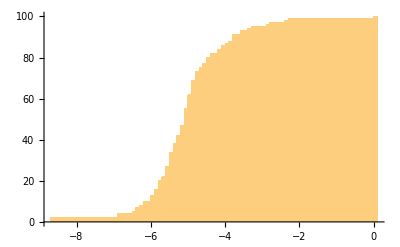

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-9.68347,0)(-8.68347,1)(-8.68347,2)(-6.8421,3)(-6.8421,4)(-6.4928,5)(-6.37267,6)(-6.37267,7)(-6.25389,8)(-6.16339,9)(-6.16339,10)(-5.9552,11)(-5.95321,12)(-5.95321,13)(-5.88195,14)(-5.83994,15)(-5.83994,16)(-5.78927,17)(-5.78927,18)(-5.77333,19)(-5.77333,20)(-5.62696,21)(-5.62696,22)(-5.57421,23)(-5.51861,24)(-5.51861,25)(-5.50391,26)(-5.50391,27)(-5.43145,28)(-5.43145,29)(-5.4298,30)(-5.4298,31)(-5.40624,32)(-5.40624,33)(-5.40204,34)(-5.35799,35)(-5.35799,36)(-5.34772,37)(-5.34772,38)(-5.25399,39)(-5.25399,40)(-5.21959,41)(-5.21959,42)(-5.12804,43)(-5.12804,44)(-5.10352,45)(-5.10202,46)(-5.10202,47)(-5.09765,48)(-5.09765,49)(-5.08128,50)(-5.08128,51)(-5.05674,52)(-5.05674,53)(-5.0006,54)(-5.0006,55)(-4.93638,56)(-4.93638,57)(-4.92345,58)(-4.91971,59)(-4.91971,60)(-4.90571,61)(-4.90571,62)(-4.87501,63)(-4.87501,64)(-4.83947,65)(-4.83947,66)(-4.81643,67)(-4.80562,68)(-4.80562,69)(-4.78846,70)(-4.78135,71)(-4.78135,72)(-4.71296,73)(-4.65303,74)(-4.65303,75)(-4.50522,76)(-4.50522,77)(-4.45148,78)(-4.43659,79)(-4.43659,80)(-4.33676,81)(-4.33676,82)(-4.11344,83)(-4.11344,84)(-4.09075,85)(-4.09075,86)(-3.96193,87)(-3.83244,88)(-3.78009,89)(-3.77816,90)(-3.77816,91)(-3.5275,92)(-3.5275,93)(-3.32429,94)(-3.27761,95)(-2.89889,96)(-2.73325,97)(-2.36805,98)(-2.21979,99)(0.,100)(0.5,100)

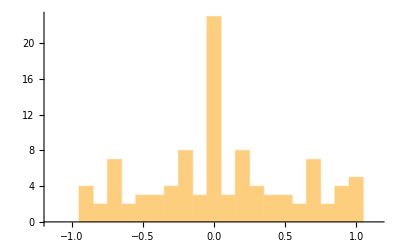

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.899629,1)(-0.88804,2)(-0.876613,3)(-0.850609,4)(-0.819452,5)(-0.751067,6)(-0.747742,7)(-0.740867,8)(-0.731212,9)(-0.718498,10)(-0.7177,11)(-0.679549,12)(-0.65965,13)(-0.604165,14)(-0.56559,15)(-0.542279,16)(-0.506044,17)(-0.450496,18)(-0.420945,19)(-0.391949,20)(-0.364673,21)(-0.324542,22)(-0.295753,23)(-0.288145,24)(-0.282342,25)(-0.237419,26)(-0.236289,27)(-0.212941,28)(-0.195421,29)(-0.188401,30)(-0.177436,31)(-0.151756,32)(-0.151633,33)(-0.109543,34)(-0.104862,35)(-0.0990645,36)(-0.0462867,37)(-0.043953,38)(-0.0314778,39)(0.,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.,56)(0.0314778,57)(0.043953,58)(0.0462867,59)(0.0990645,60)(0.104862,61)(0.109543,62)(0.151633,63)(0.151756,64)(0.177436,65)(0.188401,66)(0.195421,67)(0.212941,68)(0.236289,69)(0.237419,70)(0.282342,71)(0.288145,72)(0.295753,73)(0.324542,74)(0.364673,75)(0.391949,76)(0.420945,77)(0.450496,78)(0.506044,79)(0.542279,80)(0.56559,81)(0.604165,82)(0.65965,83)(0.679549,84)(0.7177,85)(0.718498,86)(0.731212,87)(0.740867,88)(0.747742,89)(0.751067,90)(0.819452,91)(0.850609,92)(0.876613,93)(0.88804,94)(0.899629,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Data for topic patterns

```mathematica
TopicClusters=DeleteCases[NonStopClusters,{_,_,_,"B",_,_,_,_}];
```

```mathematica
Length[TopicClusters]
```

286

```mathematica
SelectedClusters=TopicClusters;
```

```mathematica
TopicClustersDanish=TopicClusters;
```

```mathematica
Timing[PdaTopic=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{222.656,Null}

```mathematica
Timing[PdaT=Table[v=Table[prepP=PdaTopic_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,100}];v/Total[v],{m,1,100}];]
```

{0.0625,Null}

```mathematica
Timing[spec=Eigenvalues[PdaT];]
```

{1.23438,Null}

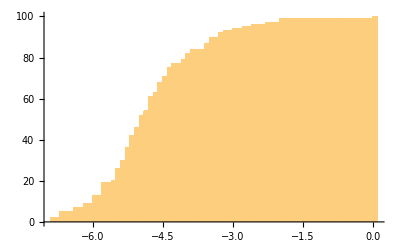

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-7.86819,0)(-6.86819,1)(-6.86819,2)(-6.67551,3)(-6.65679,4)(-6.65679,5)(-6.32437,6)(-6.32437,7)(-6.14313,8)(-6.14313,9)(-5.94456,10)(-5.94456,11)(-5.92028,12)(-5.92028,13)(-5.79916,14)(-5.79916,15)(-5.797,16)(-5.797,17)(-5.73032,18)(-5.73032,19)(-5.5991,20)(-5.47004,21)(-5.47004,22)(-5.40913,23)(-5.40913,24)(-5.40167,25)(-5.40167,26)(-5.38363,27)(-5.38363,28)(-5.32469,29)(-5.32469,30)(-5.26045,31)(-5.26045,32)(-5.25914,33)(-5.24027,34)(-5.24027,35)(-5.21648,36)(-5.19551,37)(-5.19551,38)(-5.18608,39)(-5.18608,40)(-5.16299,41)(-5.16299,42)(-5.0999,43)(-5.0999,44)(-5.07203,45)(-5.07203,46)(-4.99691,47)(-4.99691,48)(-4.96844,49)(-4.96844,50)(-4.92053,51)(-4.92053,52)(-4.8407,53)(-4.8407,54)(-4.77576,55)(-4.77576,56)(-4.77079,57)(-4.77079,58)(-4.74424,59)(-4.74424,60)(-4.71876,61)(-4.69064,62)(-4.69064,63)(-4.59212,64)(-4.59212,65)(-4.59128,66)(-4.51913,67)(-4.51913,68)(-4.47125,69)(-4.40648,70)(-4.40648,71)(-4.39071,72)(-4.39071,73)(-4.34278,74)(-4.34278,75)(-4.23317,76)(-4.23317,77)(-4.06025,78)(-4.06025,79)(-3.97037,80)(-3.97037,81)(-3.95537,82)(-3.82053,83)(-3.82053,84)(-3.59889,85)(-3.50442,86)(-3.50442,87)(-3.49904,88)(-3.49904,89)(-3.48135,90)(-3.21642,91)(-3.21642,92)(-3.18458,93)(-2.99344,94)(-2.71614,95)(-2.50608,96)(-2.24825,97)(-1.97937,98)(-1.97937,99)(0.,100)(0.5,100)

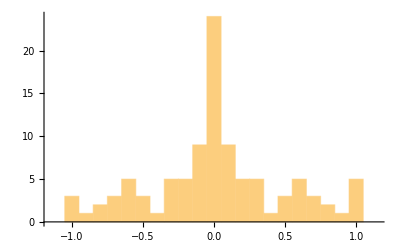

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.973465,1)(-0.958235,2)(-0.957627,3)(-0.857336,4)(-0.784473,5)(-0.774901,6)(-0.739561,7)(-0.700737,8)(-0.666176,9)(-0.645603,10)(-0.626905,11)(-0.615584,12)(-0.573893,13)(-0.570881,14)(-0.540528,15)(-0.503006,16)(-0.476366,17)(-0.449118,18)(-0.32517,19)(-0.312679,20)(-0.308276,21)(-0.307277,22)(-0.26663,23)(-0.198178,24)(-0.197032,25)(-0.175537,26)(-0.169711,27)(-0.153834,28)(-0.145754,29)(-0.141762,30)(-0.140776,31)(-0.133946,32)(-0.124106,33)(-0.106148,34)(-0.0904997,35)(-0.0888001,36)(-0.0519443,37)(-0.0481154,38)(-0.0477569,39)(-0.0325547,40)(-0.00782515,41)(-0.00632205,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.,56)(0.00632205,57)(0.00782515,58)(0.0325547,59)(0.0477569,60)(0.0481154,61)(0.0519443,62)(0.0888001,63)(0.0904997,64)(0.106148,65)(0.124106,66)(0.133946,67)(0.140776,68)(0.141762,69)(0.145754,70)(0.153834,71)(0.169711,72)(0.175537,73)(0.197032,74)(0.198178,75)(0.26663,76)(0.307277,77)(0.308276,78)(0.312679,79)(0.32517,80)(0.449118,81)(0.476366,82)(0.503006,83)(0.540528,84)(0.570881,85)(0.573893,86)(0.615584,87)(0.626905,88)(0.645603,89)(0.666176,90)(0.700737,91)(0.739561,92)(0.774901,93)(0.784473,94)(0.857336,95)(0.957627,96)(0.958235,97)(0.973465,98)(1.,99)(1.,100)(1.5,100)

### Word translation

#### Bulk vectors

```mathematica
EnglishRef=TopicClustersEnglish;
```

```mathematica
DanishRef=TopicClustersDanish;
```

```mathematica
PandPChapEnglish=StringSplit[ExampleData[{"Text","PrideAndPrejudice"}],"Chapter "~~DigitCharacter..~~" "];
```

```mathematica
Length[PandPChapEnglish]
```

61

```mathematica
VecEnglish=Table[{EnglishRef_⟦k,1⟧,StringCount[PandPChapEnglish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@EnglishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[EnglishRef]}];
```

```mathematica
PandPChapDanish=StringSplit[StringReplace[Import["Pride and Prejudice (Danish).txt"],"
\n":>""],"KAPITEL "~~DigitCharacter..];
```

```mathematica
Length[PandPChapDanish]
```

61

```mathematica
VecDanish=Table[{DanishRef_⟦k,1⟧,StringCount[PandPChapDanish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@DanishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[DanishRef]}];
```

```mathematica
FlatScreenedPairs=Flatten[Table[{#_⟦1⟧,#_⟦2,k⟧},{k,1,Length[#_⟦2⟧]}]&/@Select[Table[{EnglishRef[[k,1]],#_⟦1⟧&/@Select[VecDanish,JaccardRuzickaSim[#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧]≥Max[1-7/100*√61,1-√(Length[Select[Min[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}],#>0&]]/Total[Max[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}]])]&]},{k,1,Length[EnglishRef]}],Length[#_⟦2⟧]>0&],1];
```

```mathematica
SiftedTags=Union[(#_⟦1⟧&/@FlatScreenedPairs)];SiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SiftedTags=Union[(#_⟦2⟧&/@FlatScreenedPairs)];SiftedDanishRef=Reverse[SortBy[Table[Cases[DanishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
Length[SiftedEnglishRef]
```

124

```mathematica
Length[SiftedDanishRef]
```

123

#### Spectral parameters for English

```mathematica
FromTopics=SiftedEnglishRef;
```

```mathematica
FromDelta=ReadDelta[#]&/@FromTopics;
```

```mathematica
FromN=(#_⟦3⟧-1)&/@FromTopics;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersEnglish,PenTopic,#_⟦1⟧&/@FromTopics];]
```

{62.2816,Null}

```mathematica
FromKinQ=KinQ;
```

```mathematica
FromEta=SemanticComplexities;
```

#### Spectral parameters for Danish

```mathematica
ToTopicsDanish=SiftedDanishRef;
```

```mathematica
Length[ToTopicsDanish]
```

123

```mathematica
ToDeltaDanish=ReadDelta[#]&/@ToTopicsDanish;
```

```mathematica
ToNDanish=(#_⟦3⟧-1)&/@ToTopicsDanish;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersDanish,PdaTopic,#_⟦1⟧&/@ToTopicsDanish];]
```

{105.278,Null}

```mathematica
ToKinDanish=KinQ;
```

```mathematica
ToEtaDanish=SemanticComplexities;
```

#### Translation

```mathematica
AbsoluteTiming[fromLabeled=Transpose[{#_⟦1⟧&/@FromTopics,FromKinQ}];toLabeled=Transpose[{#_⟦1⟧&/@ToTopicsDanish,ToKinDanish}];Report=Table[{FlatScreenedPairs_⟦k⟧,(JaccardRuzickaSim[Cases[fromLabeled,{FlatScreenedPairs_⟦k,1⟧,_}]_⟦1,2⟧,Cases[toLabeled,{FlatScreenedPairs_⟦k,2⟧,_}]_⟦1,2⟧])},{k,1,Length[FlatScreenedPairs]}];]
```

{0.0202443,Null}

```mathematica
prep=Union[Select[Table[{Report_⟦n,1,1⟧,Report_⟦n,1,2⟧,Report_⟦n,2⟧},{n,1,Length[Report]}],#_⟦3⟧≥0.7&]];g=Graph[(#_⟦1⟧->#_⟦2⟧)&/@prep,EdgeWeight->(#_⟦3⟧&/@prep)];(KuhnSln={#,FindRowRank[#,prep],FindColRank[#,prep]}&/@Select[{#,PropertyValue[{g,#},EdgeWeight]}&/@FindIndependentEdgeSet[g],#_⟦2⟧>0&])//TableForm
```

{{Brighton,24}}->{{brighton,24}}
0.92337838050646 | 1 | 1
{{de,39}}->{{bourgh,35},{bourghs,4}}
0.89088453814544 | 1 | 1
{{Derbyshire,24}}->{{derbyshire,24}}
0.82024698797389 | 1 | 1
{{five,30}}->{{fem,32}}
0.91101194187528 | 1 | 1
{{impossible,44}}->{{omtumlet,1},{umulig,2},{umulighed,3},{umuligt,44}}
0.73264432405686 | 1 | 1
{{library,23}}->{{familiebibliotek,1},{lejebibliotek,2},{bibliotek,6},{biblioteket,16}}
0.92207481028797 | 1 | 1
{{town,64}}->{{london,104}}
0.84782911594065 | 1 | 1
{{Meryton,57}}->{{meryton,55},{merytonballer,1},{merytonballet,1}}
0.94953681392477 | 1 | 1
{{money,26}}->{{pengemangel,1},{pengesager,2},{pengetrang,1},{pengetransaktioner,1},{penge,20},{pengene,6},{pengenes,1}}
0.9057116701037 | 1 | 1
{{Mr,786}}->{{mr,794}}
0.85887325794504 | 1 | 1
{{Mrs,343}}->{{mrs,345}}
0.93520296595505 | 1 | 1
{{Netherfield,73}}->{{netherfield,65},{netherfieldfamilien,1},{netherfieldbal,1},{netherfieldballet,2}}
0.90834512104963 | 1 | 1
{{oh,95}}->{{sarah,1},{ah,1},{åh,68},{ih,3}}
0.90058154146864 | 1 | 1
{{park,22}}->{{park,10},{parken,17},{parkens,1}}
0.89000867585734 | 1 | 1
{{Pemberley,53}}->{{pemberley,48},{pemberleys,2},{pemberleyfamilien,1},{pemberleyfamiliens,1}}
0.87019870327696 | 1 | 1
{{pounds,24}}->{{pande,1},{pund,30}}
0.81659546566897 | 1 | 2
{{thousand,34}}->{{tusind,1},{tusinde,33}}
0.87647989251236 | 1 | 1
{{Rosings,49}}->{{rosings,49}}
0.87455099387062 | 1 | 1
{{sir,78}}->{{dydsiret,1},{sir,76}}
0.92911104291817 | 1 | 2
{{William,40},{William's,6}}->{{william,43},{williams,3}}
0.92910569323728 | 2 | 1
{{two,135}}->{{to,171}}
0.85150550283355 | 1 | 1
{{want,44}}->{{pengemangel,1},{mangel,14},{mangelfulde,1},{mangle,3},{manglede,10},{manglen,6},{manglende,6},{mangler,7},{manglerne,1},{manglet,1}}
0.81743409865998 | 1 | 1
{{agreeable,44},{agreeably,3}}->{{behag,5},{behage,11},{behagede,1},{behager,3},{behaget,2},{behagelig,23},{behagelige,9},{behageligere,3},{behageligste,3},{behageligt,10},{behagelighed,1}}
0.83445147061748 | 1 | 1
{{ball,34},{balls,8}}->{{balsal,2},{balsalen,1},{merytonballer,1},{merytonballet,1},{netherfieldbal,1},{netherfieldballet,2},{bal,23},{baller,7},{ballerne,2},{ballet,17},{bølge,1},{bølgende,1},{bolle,1}}
0.89492804820122 | 1 | 1
{{case,32},{cases,6}}->{{tilfalde,1},{tilfælde,24},{tilfældet,16},{tilfældig,2},{tilfældige,1},{tilfældighed,2},{tilfældigheder,2},{tilfældigt,4}}
0.93083989399651 | 1 | 1
{{Catherine,110},{Catherine's,16}}->{{lady,138}}
0.89335790150176 | 1 | 1
{{Charlotte,68},{Charlotte's,17}}->{{charlotte,71},{charlottes,14}}
0.89574363573821 | 1 | 1
{{Collins,156},{Collins's,24}}->{{collins,186}}
0.93172349613841 | 1 | 1
{{colonel,65},{colonel's,1}}->{{oberst,63},{obersten,1},{oberstens,1}}
0.73701160495018 | 1 | 1
{{Darcy,374},{Darcy's,44}}->{{darcy,369},{darcys,55}}
0.89937790136214 | 1 | 1
{{dinner,33},{dinners,2}}->{{familiemiddag,2},{middagsindbydelse,1},{middagsinvitation,2},{middagstid,4},{middagstraktementet,1},{middag,35},{middage,2},{middagen,15}}
0.91877616215939 | 1 | 1
{{door,32},{doors,8}}->{{dørklokken,3},{gadedør,1},{dør,4},{dur,1},{døre,4},{dyrebar,3},{døren,29},{dørene,1},{dørs,1}}
0.92071110862149 | 1 | 1
{{estate,20},{estates,4}}->{{gods,22},{godser,2},{godserne,1},{godset,1},{godsejer,2}}
0.84637783120445 | 1 | 1
{{father,116},{father's,19}}->{{gudfar,1},{hjemfaren,1},{far,85},{fars,16},{faderen,33},{faderens,5},{fædrene,1}}
0.84657381466871 | 1 | 1
{{fortnight,21},{fortnight's,2}}->{{uger,36},{ugers,1}}
0.73236948892026 | 1 | 1
{{four,33},{four-and-twenty,1}}->{{færre,1},{fire,32},{fyre,1},{fyrre,1},{fåret,1},{fyr,4},{fyrens,1}}
0.91328664325563 | 1 | 1
{{girl,38},{girls,45}}->{{kammerpigen,1},{kokkepige,1},{pigenavn,1},{stuepige,1},{stuepigen,2},{stuepiger,1},{pige,26},{pigebarn,11},{pigebørn,4},{pigebørnene,1},{piger,21},{pigerne,15}}
0.88406444973164 | 1 | 1
{{ignorance,7},{ignorant,16}}->{{uvidende,21},{uvidenhed,4},{uvidenheden,1}}
0.80803262888037 | 1 | 1
{{Jane,263},{Jane's,28}}->{{jane,282},{janes,27}}
0.83684479369418 | 1 | 1
{{Kitty,69},{Kitty's,2}}->{{kitty,66},{kittys,5}}
0.90825998007789 | 1 | 1
{{Lizzy,95},{Lizzy's,2}}->{{lizzy,95},{lizzys,1}}
0.96044714643781 | 1 | 1
{{Lydia,133},{Lydia's,38}}->{{lydia,134},{lydias,38}}
0.90338333420254 | 1 | 1
{{Mary,38},{Mary's,1}}->{{mary,38},{marys,1}}
0.83897546993825 | 1 | 1
{{mile,5},{miles,16}}->{{genmæle,1},{malplacerede,2},{mælede,2},{maler,2},{mæler,1},{malet,2},{mælet,1},{mulig,8},{mulige,3},{mile,5},{miles,17}}
0.83719321225894 | 1 | 1
{{poor,38},{poorly,3}}->{{stakkels,25}}
0.70208636759795 | 1 | 1
{{regiment,19},{regiment's,3}}->{{regiment,9},{regimentet,11},{regimentets,1},{regimentsvenner,1}}
0.88739476454196 | 1 | 1
{{room,112},{rooms,8}}->{{sædvane,1},{sædvanlig,2},{sædvanlige,14},{sædvanligt,4},{sad,41},{sidde,12},{side,53},{siddende,4},{sidder,3},{siddet,12}}
0.85439321375163 | 1 | 1
{{serious,24},{seriously,13}}->{{alvor,10},{alvoren,1},{alvorlig,14},{alvorlige,6},{alvorligere,2},{alvorligt,28}}
0.82964566737973 | 1 | 1
{{surprise,37},{surprised,35}}->{{overraske,2},{overraskede,5},{overraskedes,1},{overrasker,3},{overrasket,32}}
0.82366393647124 | 1 | 1
{{table,28},{tables,3}}->{{spillebord,2},{spillebordene,3},{spillebordet,3},{bord,8},{bordenden,3},{bordene,1},{bordet,14},{bords,4}}
0.87866741138994 | 1 | 1
{{ten,33},{tens,1}}->{{ti,31}}
0.91854217574288 | 1 | 1
{{week,29},{weeks,18}}->{{uge,25},{uges,2}}
0.75550463701267 | 1 | 1
{{Wickham,162},{Wickham's,32}}->{{wickham,169},{wickhams,27}}
0.85764536213227 | 1 | 1
{{window,16},{windows,6}}->{{butiksvindue,1},{førstesalsvindue,1},{vindue,2},{vinduer,1},{vinduerne,7},{vinduet,9}}
0.90001088970928 | 1 | 1
{{aunt,78},{aunt's,6},{aunts,1}}->{{tant,1},{tante,23},{tanten,28},{tantens,4}}
0.94708257706693 | 1 | 1
{{beautiful,15},{beauties,4},{beauty,27}}->{{smækket,1},{smukt,8},{smuk,20},{smukke,33},{smykke,1},{smykker,1},{smukkere,4},{smukkeste,4}}
0.90679951696471 | 1 | 1
{{Bennet,294},{Bennet's,29},{Bennets,10}}->{{bennetfamilien,1},{bennetsøstre,3},{bennet,292},{bennets,25}}
0.88186925286487 | 1 | 1
{{book,16},{books,13},{book-room,1}}->{{bogsamling,1},{bogsamlingens,1},{bog,13},{bogen,4},{bøger,12}}
0.7503504686042 | 1 | 1
{{child,14},{children,25},{childhood,1}}->{{barn,14},{børn,18},{barnet,2},{børnene,6}}
0.86065769451665 | 1 | 1
{{cried,91},{cry,1},{crying,2}}->{{udbrød,95},{udbrud,6},{udbryde,2}}
0.90088145600424 | 1 | 1
{{dear,158},{dearly,3},{dearest,17}}->{{kær,1},{kære,127},{kærere,1},{kæreste,16},{kærestesorg,2}}
0.93490959396792 | 1 | 1
{{Eliza,22},{Elizabeth,597},{Elizabeth's,38}}->{{elizabeth,617},{elizabeths,34}}
0.8974392379221 | 1 | 1
{{evening,72},{evening's,2},{evenings,4}}->{{aftensmåltid,1},{aftensmad,1},{aftensmaden,5},{aften,32},{aftenen,45},{aftenens,4},{aftener,4}}
0.80416608648133 | 1 | 1
{{Forster,38},{Forster's,1},{Forsters,1}}->{{forster,42}}
0.85602697278924 | 1 | 1
{{Gardiner,84},{Gardiner's,13},{Gardiners,6}}->{{gardiner,94},{gardinerne,1},{gardiners,10},{gøres,11}}
0.9170822526975 | 1 | 1
{{husband,42},{husband's,8},{husbands,4}}->{{ægtemand,26},{ægtemænd,4},{ægtemanden,14},{ægtemandens,6},{ægtemands,1}}
0.89645540974035 | 1 | 1
{{letter,115},{letters,16},{letter-paper,1}}->{{brevpapir,3},{brev,82},{breve,14},{brevene,4},{brevet,38},{brevets,2}}
0.80824731708048 | 1 | 1
{{man,145},{man's,5},{men,33}}->{{fjerdemand,1},{hofmand,1},{mand,116},{mænd,34},{manden,3},{mændene,3},{mands,7}}
0.83184692423013 | 1 | 1
{{maternal,2},{mother,110},{mother's,25}}->{{svigermor,2},{moder,2},{moderen,50},{moderens,17},{mødrene,1},{mor,60},{mors,10}}
0.87704310061909 | 1 | 1
{{motion,1},{motive,17},{motives,7}}->{{bevæggrund,11},{bevæggrunde,7},{bevæggrunden,1},{bevæge,3},{bevægede,1},{bevæger,1},{bevæges,2},{bevæget,2},{bevågenhed,1}}
0.85670199178681 | 1 | 1
{{nephew,20},{nephew's,2},{nephews,2}}->{{nevø,15},{nevøen,4},{nevøens,3},{nevøer,2},{nevøs,2}}
0.85512464206849 | 1 | 1
{{niece,20},{niece's,2},{nieces,9}}->{{yndlingsniece,1},{niece,14},{niecen,7},{niecer,6},{niecerne,3},{nieces,1}}
0.92932867177225 | 1 | 1
{{Phillip's,1},{Phillips,26},{Phillips's,5}}->{{philips,34}}
0.91878067791261 | 1 | 1
{{read,40},{reading,14},{reader,3}}->{{genlæse,1},{genlæste,1},{læs,2},{løs,2},{læse,15},{læser,7},{læses,1},{løses,1},{last,4},{læst,12},{løst,2},{læste,20},{liste,2},{laster,1}}
0.81574401294578 | 1 | 1
{{sore,1},{sorely,1},{sorry,34}}->{{ked,37},{kede,2}}
0.83421642388816 | 1 | 1
{{uncle,59},{uncle's,9},{uncles,3}}->{{morskab,7},{morsomt,4},{moralsk,6},{moralske,1},{more,8},{morede,4},{morer,5},{moret,1},{morbroderen,19},{morbroderens,3},{morbrødre,1},{morbror,35},{morbrors,6}}
0.87410177157382 | 1 | 1
{{wife,44},{wife's,3},{wives,1}}->{{truede,1},{hustru,36},{hustruen,6},{hustruens,2},{hustrus,3}}
0.90448507337056 | 1 | 1
{{year,28},{years,33},{years',2}}->{{årsag,12},{årvågen,1},{årstiden,2},{årstidens,1},{årsagen,6},{årsager,2},{årsagerne,1},{år,61},{året,16},{årets,1},{års,8}}
0.85409761999389 | 1 | 1
{{young,130},{younger,30},{youngest,13}}->{{ung,56},{yngre,11},{unge,72}}
0.91574602323174 | 1 | 1
{{best,41},{better,92},{good,184},{good-humoured,6}}->{{godhjertede,2},{godhjertet,1},{godhjertethed,1},{bedre,76},{bedst,8},{bedste,37},{god,47},{gode,58},{godeste,5},{godt,180}}
0.85867494164847 | 1 | 1
{{Bingley,257},{Bingley's,49},{Bingleys,4},{Bingleys',1}}->{{bingleyfamilien,1},{bingleysøstrene,1},{bingley,271},{bingleys,45}}
0.8985775532564 | 1 | 1
{{brother,62},{brotherly,2},{brother's,13},{brothers,2}}->{{broderen,18},{broderens,11},{brødre,1},{bror,32},{brors,3},{morbroderen,19},{morbroderens,3},{morbrødre,1},{morbror,35},{morbrors,6}}
0.8076148314782 | 1 | 1
{{complied,4},{compliment,26},{compliments,11},{compliance,1}}->{{kompliment,17},{komplimenten,3},{komplimenter,8},{komplimentere,1},{komplimenterede,5},{komplimenteres,1}}
0.79187371879128 | 1 | 1
{{daily,3},{day,130},{day's,4},{days,30}}->{{dag,95},{dage,30},{dagen,40},{dagene,3},{dagens,3},{dages,2},{dags,7}}
0.89386123974865 | 1 | 1
{{dance,31},{danced,12},{dances,10},{dancing,21}}->{{dans,9},{danse,33},{dansede,14},{dansen,6},{dansende,3},{danser,7},{danset,4}}
0.88974336709843 | 1 | 1
{{daughter,78},{daughter's,7},{daughters,49},{daughters',1}}->{{datter,55},{døtre,43},{datteren,17},{datterens,6},{dateret,2},{døtrene,9},{døtrenes,2},{datters,5},{døtres,2}}
0.9199022685533 | 1 | 1
{{fortune,39},{fortunes,1},{fortunate,15},{fortunately,2}}->{{formue,27},{formuende,3}}
0.89668921185774 | 1 | 1
{{honour,42},{honoured,9},{honours,2},{honourable,6}}->{{ærværdige,1},{ære,54},{ærefuld,1},{ure,1},{ærede,2},{æren,4},{uret,5},{urette,1}}
0.87685219875663 | 1 | 1
{{Lucas,65},{Lucas's,5},{Lucases,13},{Lucases',1}}->{{lucas,79},{lucasfamilien,3}}
0.90177684963382 | 1 | 1
{{send,24},{sending,1},{sends,1},{sent,20}}->{{send,2},{sende,16},{sender,7},{sendes,2},{sendt,18},{sendte,8}}
0.87654647610307 | 1 | 1
{{turn,27},{turned,43},{turning,13},{turns,2}}->{{vende,16},{vender,4},{vendt,11},{vendte,54}}
0.83568504888732 | 1 | 1
{{vanish,1},{vanished,2},{vain,20},{vanity,18}}->{{forfængelig,3},{forfængelige,1},{forfængelighed,16},{forfængeligheden,1}}
0.80635482923145 | 1 | 1
{{admire,18},{admired,12},{admires,2},{admiring,2},{admirer,3}}->{{beundre,9},{beundrede,14},{beundrende,1},{beundrer,4},{beundrerinde,1},{beundret,3}}
0.80204429044731 | 1 | 1
{{believed,37},{believing,12},{belief,15},{believe,87},{believes,1}}->{{trofast,1},{trofaste,1},{trofasthed,2},{tro,84},{troede,21},{troen,3},{troet,18},{tror,85},{troværdig,1},{troværdige,1},{troværdigheden,1},{troværdigt,1}}
0.79760768566862 | 1 | 1
{{carriage,44},{carriages,6},{carried,8},{carry,5},{carrying,4}}->{{vogne,7},{vogn,13},{vognen,35},{vognens,1},{vogns,1}}
0.86780420484674 | 1 | 1
{{comfort,31},{comforted,1},{comforts,4},{comfortable,12},{comfortably,2}}->{{monstro,2},{vantro,5},{trøst,32},{trøste,14},{trøstede,1},{trøstende,1},{trøstens,1},{trøster,3},{trøstet,1}}
0.89170932647056 | 1 | 1
{{deserve,9},{deserved,6},{deservedly,1},{deserves,4},{deserving,2}}->{{fortjener,10},{fortjent,10},{fortjente,6},{fortjenstfulde,1},{fortjenstfuldhed,2},{fortjenstfuldt,1},{fortjeneste,2},{fortjenester,1}}
0.85459806412807 | 1 | 1
{{disappoint,2},{disappointed,12},{disappointing,3},{disappointment,17},{disappointments,1}}->{{skaffe,6},{skuffe,4},{skaffede,2},{skuffede,1},{skaffet,1},{skuffet,11},{skuffelse,12},{skuffelsen,2},{skuffelser,3}}
0.88389847136653 | 1 | 1
{{house,106},{houses,4},{household,1},{housemaid,2},{housemaids,1}}->{{husholdning,3},{pakhuse,1},{hus,24},{huse,3},{huset,43},{husets,5},{hustru,36},{hustruen,6},{hustruens,2},{hustrus,3}}
0.76609112267469 | 1 | 1
{{length,32},{long,114},{longed,9},{longing,2},{longer,44}}->{{ønskværdig,3},{ønskværdige,2},{ønskværdigt,5},{ønske,94},{ønskede,51},{ønsker,55},{ønsket,19}}
0.8374612266461 | 1 | 1
{{miss,283},{missed,3},{missing,1},{missent,2},{missish,1}}->{{miss,264}}
0.86409127813918 | 1 | 1
{{pain,28},{painful,14},{painfully,2},{paining,1},{pains,4}}->{{smerte,23},{smertefuld,2},{smertefulde,1},{smertefuldt,2},{smerten,4},{smerter,2},{smertelig,1},{smertelige,2},{smerteligere,1},{smerteligt,6}}
0.81189736568965 | 1 | 1
{{pride,47},{prided,1},{proud,22},{proudly,1},{proudest,1}}->{{stolt,26},{stolte,3},{stolthed,40},{stoltheden,2}}
0.91518162134349 | 1 | 1
{{talk,32},{talked,38},{talking,39},{talks,1},{talker,1}}->{{talt,32},{tålt,1},{talte,78},{tålte,2}}
0.81893928950527 | 2 | 1
{{speak,66},{speaking,33},{speaks,3},{speaker,1},{spoke,43},{spoken,16},{spokesman,1}}->{{enetaler,1},{takketaler,1},{talefod,1},{talegaver,1},{tal,3},{tale,110},{tåle,5},{taler,19},{tåler,5},{tales,1},{tåles,1},{tåls,1}}
0.83900721481099 | 1 | 2
{{woman,55},{womanly,1},{woman's,4},{women,19},{women's,1}}->{{kvindetøj,1},{kvinde,54},{kvinder,21},{kvinders,2},{kvindes,5},{kvindesindets,1},{kvindeblikke,1}}
0.81683573093258 | 1 | 1
{{choice,15},{choose,19},{chooses,8},{choosing,1},{chose,16},{chosen,8}}->{{valg,9},{vælg,2},{vælge,10},{vælger,3},{valgt,7},{valgte,10}}
0.93950358442058 | 1 | 1
{{marriage,66},{married,61},{marry,42},{marrying,23},{matrimonial,1},{matrimony,6}}->{{giftes,12},{gift,59},{gifte,42},{giftede,1},{gifter,7},{giftet,4}}
0.88821187619055 | 1 | 1
{{neighbour,8},{neighbouring,2},{neighbours,10},{neighbours',1},{neighbourhood,29},{neighbourhoods,1}}->{{naboskab,1},{nabolag,1},{nabolaget,16},{nabolagets,3},{nabo,5},{naboer,8},{naboerne,2},{naboernes,2}}
0.7144967426918 | 1 | 1
{{office,6},{officer,8},{officers,29},{officers',2},{officiousness,1},{officious,3}}->{{officer,6},{officeren,1},{officerer,14},{officererne,15},{officerernes,1}}
0.7203625189169 | 1 | 1
{{visit,51},{visited,4},{visiting,5},{visits,5},{visitor,11},{visitors,14}}->{{besøg,57},{besøge,9},{besøgende,1},{besøgene,2},{besøger,2},{besøget,12},{besøgets,1},{besøgt,5},{besøgte,2}}
0.85812998913148 | 1 | 1
{{write,39},{writes,1},{writing,12},{written,19},{writer,3},{wrote,21}}->{{skrev,28},{skriv,4},{skrive,41},{skrevet,20},{skrevne,1},{skriver,20},{skrives,2}}
0.91200061571446 | 1 | 1
{{intend,3},{intended,21},{intending,7},{intention,15},{intentionally,2},{intentions,6},{intently,2}}->{{hensigt,50},{hensigten,3},{hensigter,5}}
0.87765967524863 | 1 | 1
{{gentle,5},{gentleness,4},{gentlemen,34},{gentlemen's,3},{gentleman,32},{gentleman's,8},{gentlemanlike,8},{gentlest,1},{gentlewoman,1}}->{{herre,46},{herren,5},{herrens,3},{herrer,16},{herrerne,22},{herrernes,1},{herres,8}}
0.867108008195 | 1 | 1
{{relate,11},{related,16},{relates,3},{relating,5},{relation,11},{relations,22},{relations',2},{relationship,12},{relative,3}}->{{fortalt,22},{fortalte,35}}
0.82272546737541 | 1 | 1

```mathematica
ResiftedTags=Union[(#_⟦1⟧&/@prep)];ResiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
ResiftedTags=Union[(#_⟦2⟧&/@prep)];ResiftedDanishRef=Reverse[SortBy[Table[Cases[DanishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SemanticSim={Position[ResiftedEnglishRef,{#_⟦1⟧,___}]_⟦1,1⟧,Position[ResiftedDanishRef,{#_⟦2⟧,___}]_⟦1,1⟧,#_⟦3⟧}&/@prep;
```

```mathematica
OptimalNodes={Position[ResiftedEnglishRef,{#_⟦1,1,1⟧,___}]_⟦1,1⟧,Position[ResiftedDanishRef,{#_⟦1,1,2⟧,___}]_⟦1,1⟧,#_⟦2,1,1⟧,#_⟦3,1,1⟧}&/@KuhnSln;
```

```mathematica
Export["PnP_EnglishDanish.txt","%tournament\n"<>StringJoin[Riffle[Flatten["\\put("<>ToString[1.5+1+4#_⟦2⟧]<>","<>ToString[90-4#_⟦1⟧]<>"){\\color[rgb]"<>ToString[TempRGB[#_⟦3⟧]]<>"{\\rule{4pt}{4pt}}}"&/@SemanticSim],"\n"]]<>"\n%crosshairs\n"<>StringJoin[Riffle["\n%"<>ResiftedEnglishRef[[#_⟦1⟧,1,1,1]]<>"_"<>ResiftedDanishRef[[#_⟦2⟧,1,1,1]]<>"
\\put("<>ToString[1.5+4#_⟦2⟧+3]<>","<>ToString[90-4#_⟦1⟧+2]<>"){\\color{green}\\linethickness{"<>ToString[1.5/#_⟦3⟧]<>"pt}\\line(-1,0){"<>ToString[4#_⟦2⟧-2]<>"}\\linethickness{"<>ToString[1.5/#_⟦4⟧]<>"pt}\\line(0,1){"<>ToString[4#_⟦1⟧-2]<>"}}"&/@OptimalNodes,"\n"]]];
```

#### English labels

```mathematica
FromClusters=ResiftedEnglishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EnglishCompress[w_]:=StringReplace[w,{"ai":>"𝔸","ea":>"𝕀","ou":>"𝕌","ee":>"𝔼","oo":>"𝕆"}]
```

```mathematica
EnglishDecompress[w_]:=StringReplace[w,{"𝔸":>"ai","𝕀":>"ea","𝕌":>"ou","𝔼":>"ee","𝕆":>"oo"}]
```

```mathematica
EvenOut[cl_]:=(prep=EnglishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,EnglishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["EnglishLabels_for_Danish_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5-3Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[91.75-1.5-4k]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

#### Danish labels

```mathematica
FromClusters=ResiftedDanishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
DanishSort[WordFreqList_]:=Transpose[(assoc=<|#_⟦1⟧->#_⟦2⟧&/@Transpose[WordFreqList]|>;{#,assoc[#]}&/@AlphabeticSort[Keys[assoc],"Danish"])]
```

```mathematica
DanishDoublets=Alternatives@@(#<>#&/@CharacterRange["a","z"])
```

aa|bb|cc|dd|ee|ff|gg|hh|ii|jj|kk|ll|mm|nn|oo|pp|qq|rr|ss|tt|uu|vv|ww|xx|yy|zz

```mathematica
DanishCompress[w_]:=(Lprot=Max[0,Max[Flatten[StringLength/@StringCases[w," "..]]]];StringTake[#,UpTo[Lprot]]<>StringReplace[StringDrop[#,UpTo[Lprot]],{(x:DanishDoublets):>ToUpperCase[StringTake[x,1]]}]&/@w)
```

```mathematica
DanishDecompress[w_]:=StringReplace[w,{X:Alternatives@@CharacterRange["A","Z"]:>ToLowerCase[X]<>ToLowerCase[X]}]
```

```mathematica
PadPrefix[cl_]:=DanishSort[RefString=Last[SortBy[cl_⟦1⟧,StringLength[#]&]];Transpose[Table[prep=SequenceAlignment[RefString,cl_⟦1,n⟧];If[Length[prep_⟦1⟧]>1,Lmax=Max[StringLength/@prep_⟦1⟧];{Table[" ",{m,1,Lmax-StringLength[prep_⟦1,2⟧]}]<>cl_⟦1,n⟧,cl_⟦2,n⟧},{cl_⟦1,n⟧,cl_⟦2,n⟧}],{n,1,Length[cl_⟦1⟧]}]]]
```

```mathematica
ClusterCount={{"dætter","dætters","døtre","guddætter"},{10,72,83,100}}
```

{{dætter,dætters,døtre,guddætter},{10,72,83,100}}

```mathematica
EvenOut[cl_]:=(prep0=PadPrefix[cl];prep=DanishCompress[prep0_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,prep0_⟦2⟧}])
```

```mathematica
EvenOut[ClusterCount]
```

{{   dæTer ,10},{   dæTers,72},{   døtre ,83},{guddæTer ,100}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,DanishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
 
10 | 2
 
10 | 3
 
10 | 4
d
10 | 5
æ
10 | 6
tt
10 | 7
e
10 | 8
r
10 | 9
 
10
1
 
72 | 2
 
72 | 3
 
72 | 4
d
72 | 5
æ
72 | 6
tt
72 | 7
e
72 | 8
r
72 | 9
s
72
1
 
83 | 2
 
83 | 3
 
83 | 4
d
83 | 5
ø
83 | 6
t
83 | 7
r
83 | 8
e
83 | 9
 
83
1
g
100 | 2
u
100 | 3
d
100 | 4
d
100 | 5
æ
100 | 6
tt
100 | 7
e
100 | 8
r
100 | 9
 
100

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{9, ,10},{9,s,72},{9, ,83},{9, ,100}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
 
10 | 1
 
72 | 1
 
83 | 1
g
100
2
 
10 | 2
 
72 | 2
 
83 | 2
u
100
3
 
10 | 3
 
72 | 3
 
83 | 3
d
100
4
d
10 | 4
d
72 | 4
d
83 | 4
d
100
5
æ
10 | 5
æ
72 | 5
ø
83 | 5
æ
100
6
tt
10 | 6
tt
72 | 6
t
83 | 6
tt
100
7
e
10 | 7
e
72 | 7
r
83 | 7
e
100
8
r
10 | 8
r
72 | 8
e
83 | 8
r
100
9
 
10 | 9
s
72 | 9
 
83 | 9
 
100

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
g
100 | 1
 
165 | 
2
u
100 | 2
 
165 | 
3
d
100 | 3
 
165 | 
4
d
265 |  | 
5
æ
100 | 5
ø
83 | 5
æ
82
6
tt
100 | 6
t
83 | 6
tt
82
7
e
100 | 7
r
83 | 7
e
82
8
r
100 | 8
e
83 | 8
r
82
9
 
183 | 9
s
72 | 9
 
10

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{6},tt,100,0},{{6},t,83,100},{{6},tt,82,183}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["DanishLabels_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5.25-.25+1+4k]<>","<>ToString[91]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BCR{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=StringReplace[ToUpperCase[StringReplace[BCData_⟦m,n,2⟧,"ß":>"𝕊"]],"𝕊":>"ß"];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Å":>"Ç"}];RemoveDiacritics[temp1,Language->"Danish"]==temp1,1,1.35],10^-3]]])<>"}{"<>(If[StringDelete[temp,CharacterRange["A","Z"]]=="",temp,StringReplace[StringReplace[StringReplace[ExportString[temp,"TeX"],{"\\ss":>"{\\ss}","\\AA":>"Å"}],___~~"\\[\\text{":>""],"}\\]"~~___:>""]])<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

```mathematica
Export["EnglishDanish_Report.txt",{Last[SortBy[#_⟦1,1,1⟧,Last]]_⟦1⟧,Last[SortBy[#_⟦1,1,2⟧,Last]]_⟦1⟧}&/@KuhnSln];
```